```mathematica
eqs={k*(G+n-1)-ga*Fm/Fp*Cos[2*ψ]-gp*Fm/Fp*Sin[2*ψ],-w+a*k*(G+n-1)+ga*Fm/Fp*Sin[2*ψ]-gp*Fm/Fp*Cos[2*ψ],k*(G-n-1)-ga*Fp/Fm*Cos[2*ψ]+gp*Fp/Fm*Sin[2*ψ],-w+a*k*(G-n-1)-ga*Fp/Fm*Sin[2*ψ]-gp*Fp/Fm*Cos[2*ψ],g*Λ-g*G-G*(Fp^2+Fm^2)-n*(Fp^2-Fm^2),-gd*n-G*(Fp^2-Fm^2)-n*(Fp^2+Fm^2)};
vars={Fp,Fm,ψ,w,G,n}
```

{Fp,Fm,ψ,w,G,n}

```mathematica
Solve[eqs==0,vars, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{k (-1+G+n)-(Fm ga Cos[2 ψ])/Fp-(Fm gp Sin[2 ψ])/Fp,a k (-1+G+n)-w-(Fm gp Cos[2 ψ])/Fp+(Fm ga Sin[2 ψ])/Fp,k (-1+G-n)-(Fp ga Cos[2 ψ])/Fm+(Fp gp Sin[2 ψ])/Fm,a k (-1+G-n)-w-(Fp gp Cos[2 ψ])/Fm-(Fp ga Sin[2 ψ])/Fm,-(Fm^2+Fp^2) G-g G-(-Fm^2+Fp^2) n+g Λ,-(-Fm^2+Fp^2) G-(Fm^2+Fp^2) n-gd n}==0,{Fp,Fm,ψ,w,G,n},ℝ]

```mathematica
tst={x+y-2,x-y-5}
```

{-2+x+y,-5+x-y}

```mathematica
Solve[tst==0,{x,y}]
```

{{x→7/2,y→-3/2}}

```mathematica
tst==0
```

{-2+x+y,-5+x-y}==0

## Test of formulae

```mathematica
(*Parameters*)
a=2;
k=300;
g=1;
gd=50;
ga=-0.01;
gp=34.611;
Λ=1.8;

a=5;
k=1000;
g=1;
gd=1/(5*10^-3);
ga=-0.000001;
gp=0.1;
Λ=1.6;
```

```mathematica
Clear[a,k,g,gd,ga,gp,Λ];
```

```mathematica
equations={(g*(Λ-G)*G+gd*n^2)*((G-1)*(ga^2+gp^2)+A)/(2*n*gp*(gp-a*ga))-g*(Λ-G)*n+gd*G*n,
k^2*((G-1)*(2*ga*gp+a*(gp^2-ga^2))-a*A)/ga/gp-((G-1)*(ga^2+2*a*ga*gp-gp^2)-A)/((G-1-n)*(G-1+n))};
Asub={A-> -Sqrt[(G-1)^2*(ga^2+gp^2)^2-4*n^2*ga*gp*(ga+a*gp)*(gp-a*ga)]};
```

```mathematica
solution=Solve[(equations/.Asub)==0,{G,n},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{G→0.505534,n→-0.494466},{G→0.505534,n→0.494466},{G→0.996967,n→-0.00303351},{G→0.996967,n→0.00303351},{G→1.,n→-3.11001×10^-12},{G→1.,n→3.11001×10^-12},{G→1.,n→-5.59517×10^-11},{G→1.,n→5.59517×10^-11},{G→1.,n→-1.5044×10^-7},{G→1.,n→1.5044×10^-7}}

```mathematica
ind=7;
sol=Join[solution[[ind]],
{Fp-> (Sqrt[(g*(Λ-G)-gd*n)/(2*(G+n))]/.solution[[ind]]),
Fm-> (Sqrt[(g*(Λ-G)+gd*n)/(2*(G-n))]/.solution[[ind]]),
ψ-> (1/2*ArcTan[((G-1)*(ga^2+gp^2)+A)/(2*n*gp*(ga+a*gp))]/.Asub/.solution[[ind]]),
w-> (k/ga*(-(G-1)*(gp-a*ga)+n*(ga+a*gp)*((G-1)*(ga^2+gp^2)+A)/(2*n*gp*(ga+a*gp)))/.Asub/.solution[[ind]])
}
]
```

{G→1.,n→-5.59517×10^-11,Fp→0.547723,Fm→0.547723,ψ→2.79773×10^-7,w→0.100005}

```mathematica
eqs/.sol//MatrixForm//Chop
```

(0.00998092
-34.711
0.0100197
-34.711
0.2
-8.39276×10^-9)

## Roman Approach

```mathematica
ClearAll["Global`*"]
```

```mathematica
eq1=κ(G+d - 1)-γa Sqrt[qm/qp] Cos[2 ψ]- γp Sqrt[qm/qp]Sin[2 ψ];
eq2= κ  α(G+d - 1)+γa Sqrt[qm/qp] Sin[2 ψ]-γp Sqrt[qm/qp]Cos[2 ψ]-ω;
eq3=κ (G-d - 1)-γa Sqrt[qp/qm]Cos[2 ψ]+ γp Sqrt[qp/qm] Sin[2 ψ];
eq4=κ  α(G-d - 1)-γa Sqrt[qp/qm]Sin[2 ψ]-γp Sqrt[qp/qm]Cos[2 ψ]-ω;
eq5=-γ(G -Λ)-γ(G+d) qp-γ(G-d) qm;
eq6=-γd d-γ(G+d) qp+γ(G-d) qm;

solGd=Solve[{eq5==0,eq6==0},{G,d}][[1]]
```

{G→((qm γ+qp γ+γd) Λ)/(qm γ+qp γ+4 qm qp γ+γd+qm γd+qp γd),d→((qm-qp) γ Λ)/(qm γ+qp γ+4 qm qp γ+γd+qm γd+qp γd)}

```mathematica
(eq2-α*eq1)/.solGd//FullSimplify//Solve[#==0,ω]&//FullSimplify
Solve[(eq4-α*eq3/.solGd)==0,ω]//FullSimplify
Solve[(eq4/.solGd)==0,ω]//FullSimplify
```

{{ω→√(qm/qp) ((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])}}

{{ω→√(qp/qm) ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ])}}

{{ω→α κ (-1+((2 qp γ+γd) Λ)/(γd+qp (γ+γd)+qm (γ+4 qp γ+γd)))-√(qp/qm) (γp Cos[2 ψ]+γa Sin[2 ψ])}}

```mathematica
(*cosinsubs={Cos[2ψ]->a,Sin[2ψ]->Sqrt[1-a^2]};*)
cosinsubs={Sin[2ψ]->aa,Cos[2ψ]->Sqrt[1-aa^2]};
(*cosinsubs={Sin[2ψ]->2*a/(1+a^2),Cos[2ψ]->(1-a^2)/(1+a^2)};*)
solω1=Simplify[Solve[(eq2/.cosinsubs/.solGd)==0,ω],Assumptions->qm>0&&qp>0&&-1<aa<1][[1,1]];
solω2=Simplify[Solve[(eq4/.cosinsubs/.solGd)==0,ω],Assumptions->qm>0&&qp>0&&-1<a<1][[1,1]];
Eq1=(eq1/.cosinsubs/.solGd);
Eq2=(eq3/.cosinsubs/.solGd);
Eq3=Simplify[(eq2-eq4)/.cosinsubs/.solGd,Assumptions->qm>0&&qp>0&&aa<1&&aa>-1];
```

```mathematica
{Eq1,Eq2,Eq3}//FullSimplify//MatrixForm
```

(-√(qm/qp) (√(1-aa^2) γa+aa γp)+κ (-1+((2 qm γ+γd) Λ)/(γd+qp (γ+γd)+qm (γ+4 qp γ+γd)))
√(qp/qm) (-√(1-aa^2) γa+aa γp)+κ (-1+((2 qp γ+γd) Λ)/(γd+qp (γ+γd)+qm (γ+4 qp γ+γd)))
(aa (qm+qp) γa)/(√(qm qp))+(-√(-((-1+aa^2) qm)/qp)+√(-((-1+aa^2) qp)/qm)) γp+(2 (qm-qp) α γ κ Λ)/((qm+qp+4 qm qp) γ+(1+qm+qp) γd))

```mathematica
γa=-0.016*2*Pi;
γ=1.;
γp=8.*2*Pi;
κ=1000.;
γd=50;
α=6.;
Λ=3.;
qp0=0.9;
qm0=0.1;
a0=0.1;

γa=-0.01;
γ=1.;
γp=53.366992312063097;
κ=300.;
γd=50.;
α=3.;
Λ=5;
qp0=0.9;
qm0=0.1;
a0=-0.1;

solQpm=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{qm,qm0,N[10^-8],3},{qp,qp0,N[10^-8],3},{aa,a0,-1.,1.}}]
solGd/.solQpm;
(Abs[d]/.%)≥ (G-1)/.%
solω1/.solQpm;
solω2/.solQpm;
```

FindRoot::reged: The point {0.51453,3.,-0.221365} is at the edge of the search region {1.×10^-8,3.} in coordinate 2 and the computed search direction points outside the region.

{qm→0.51453,qp→3.,aa→-0.221365}

False

```mathematica
solQpm2=NSolve[{Eq1==0,Eq2==0,Eq3==0},{qm,qp,aa}]
```

{{qm→2.18905-6.00002 ⅈ,qp→2.18905+6.00002 ⅈ,aa→0.-2.25602 ⅈ},{qm→2.18905+6.00002 ⅈ,qp→2.18905-6.00002 ⅈ,aa→0.+2.25602 ⅈ},{qm→0.704709,qp→3.26387,aa→-0.210277},{qm→0.704709,qp→3.26387,aa→-0.210277},{qm→3.26387,qp→0.704709,aa→0.210277},{qm→2.00008,qp→2.00008,aa→0},{qm→2.00008,qp→2.00008,aa→0}}

```mathematica
solSel=solQpm2//Select[#,AllTrue[{qm,qp,aa}/.#,#∈Reals&]&]&
```

{{qm→0.704709,qp→3.26387,aa→-0.210277},{qm→0.704709,qp→3.26387,aa→-0.210277},{qm→3.26387,qp→0.704709,aa→0.210277},{qm→2.00008,qp→2.00008,aa→0},{qm→2.00008,qp→2.00008,aa→0}}

```mathematica
solSel//Select[#,(Abs[qp-qm]/.#)<10^-6&]&
```

{{qm→2.00008,qp→2.00008,aa→0},{qm→2.00008,qp→2.00008,aa→0}}

```mathematica
Length[emp]
```

0

```mathematica
answrs={qp,qm,ArcSin[a]/2,ω,G,d}/.solω1/.solGd/.solQpm;
answrs//MatrixForm
```

(3.
0.51453
-0.111607
53.8761
1.1366
-0.052789)

```mathematica
sol=Flatten[{solGd/.solQpm,solQpm,solω1/.solQpm}]
```

{G→1.0141,d→-0.0305558,qm→0.937207,qp→2.5488,a→-0.152396,ω→-46.7952}

```mathematica
matmat=(M//TrigReduce)/.cosinsubs/.{Gs-> G, ds-> d,Qp-> qp,Qm-> qm}/.sol
```

{{-0.0100001,-53.367,0.0100002,53.367,321.934,321.934},{53.367,-0.0100001,-53.367,0.0100002,965.801,965.801},{0.00999981,53.367,-0.00999987,-53.367,321.934,-321.934},{-53.367,0.00999981,53.367,-0.00999987,965.801,-965.801},{-2.14615,0,-2.14615,0,-3.30314,-3.05587×10^-8},{-2.14615,0,2.14615,0,-3.05587×10^-8,-52.3031}}

```mathematica
{Eq1,Eq2,Eq3}/.solGd/.solQpm//MatrixForm
{eq5,eq6}/.solGd/.solQpm//MatrixForm
```

(-9.77343×10^-15
1.19748×10^-14
1.75689×10^-15)

(2.22045×10^-16
0.)

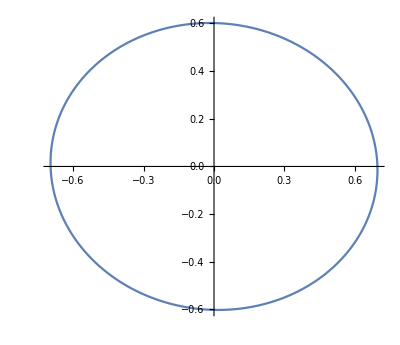

```mathematica
Ep =answrs[[1]];
Em = answrs[[2]];
p =answrs[[3]];
ParametricPlot[{Re[(Ep*Exp[I*(t+p)]+Em*Exp[I*(t-p)])/Sqrt[2]],Re[(Ep*Exp[I*(t+p)]-Em*Exp[I*(t-p)])/Sqrt[2]/I]},{t,0,2π}]
```

## Linearization

```mathematica
ClearAll["Global`*"];
eq1=κ(1+I α)(G+d-1)Fp-(γa+I γp)Fm;
eq2=κ(1+I α)(G-d-1)Fm-(γa+I γp)Fp;
eq3=γ(Λ-G)-γ G(Abs[Fp]^2+Abs[Fm]^2)-γ d (Abs[Fp]^2-Abs[Fm]^2);
eq4=-γd d-γ G(Abs[Fp]^2-Abs[Fm]^2)-γ d (Abs[Fp]^2+Abs[Fm]^2);
eqns={eq1,eq2,eq3,eq4};
linsub={Fp-> (Sqrt[Qp]+ap)*Exp[I ω t+I ψ],Fm-> (Sqrt[Qm]+am)*Exp[I ω t-I ψ], G-> Gs+Δ,d-> ds+δ};
statsub={Fp-> Sqrt[Qp]*Exp[I ω t+I ψ],Fm-> Sqrt[Qm]*Exp[I ω t-I ψ], G-> Gs,d-> ds};
eqsub={(eq1/.statsub)-ω*Exp[I ω t+I ψ]-> 0, (eq2/.statsub)-ω*Exp[I ω t-I ψ]-> 0,(eq3/.statsub//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&//Expand)-> 0,(eq4/.statsub//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&//Expand)-> 0};
v2diff={ap,am,Δ,δ};
```

```mathematica
mults={Exp[I ω t+I ψ],Exp[I ω t-I ψ],1,1};
addrights={(Sqrt[Qp]+ap)*Exp[I ω t+I ψ]*I*ω,(Sqrt[Qm]+am)*Exp[I ω t-I ψ]*I*ω,0,0};
lineqs=Table[((eqns[[i]]/.linsub)-addrights[[i]])/mults[[i]]//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&//Expand,{i,1,4}]
```

{-am ⅇ^(-2 ⅈ ψ) γa-ⅇ^(-2 ⅈ ψ) √Qm γa-ⅈ am ⅇ^(-2 ⅈ ψ) γp-ⅈ ⅇ^(-2 ⅈ ψ) √Qm γp-ap κ+ap ds κ+ap Gs κ-√Qp κ+ds √Qp κ+Gs √Qp κ-ⅈ ap α κ+ⅈ ap ds α κ+ⅈ ap Gs α κ-ⅈ √Qp α κ+ⅈ ds √Qp α κ+ⅈ Gs √Qp α κ+ap δ κ+√Qp δ κ+ⅈ ap α δ κ+ⅈ √Qp α δ κ+ap Δ κ+√Qp Δ κ+ⅈ ap α Δ κ+ⅈ √Qp α Δ κ-ⅈ ap ω-ⅈ √Qp ω,-ap ⅇ^(2 ⅈ ψ) γa-ⅇ^(2 ⅈ ψ) √Qp γa-ⅈ ap ⅇ^(2 ⅈ ψ) γp-ⅈ ⅇ^(2 ⅈ ψ) √Qp γp-am κ-am ds κ+am Gs κ-√Qm κ-ds √Qm κ+Gs √Qm κ-ⅈ am α κ-ⅈ am ds α κ+ⅈ am Gs α κ-ⅈ √Qm α κ-ⅈ ds √Qm α κ+ⅈ Gs √Qm α κ-am δ κ-√Qm δ κ-ⅈ am α δ κ-ⅈ √Qm α δ κ+am Δ κ+√Qm Δ κ+ⅈ am α Δ κ+ⅈ √Qm α Δ κ-ⅈ am ω-ⅈ √Qm ω,-Gs γ-γ Δ+γ Λ+ds γ Abs[am+√Qm]^2-Gs γ Abs[am+√Qm]^2+γ δ Abs[am+√Qm]^2-γ Δ Abs[am+√Qm]^2-ds γ Abs[ap+√Qp]^2-Gs γ Abs[ap+√Qp]^2-γ δ Abs[ap+√Qp]^2-γ Δ Abs[ap+√Qp]^2,-ds γd-γd δ-ds γ Abs[am+√Qm]^2+Gs γ Abs[am+√Qm]^2-γ δ Abs[am+√Qm]^2+γ Δ Abs[am+√Qm]^2-ds γ Abs[ap+√Qp]^2-Gs γ Abs[ap+√Qp]^2-γ δ Abs[ap+√Qp]^2-γ Δ Abs[ap+√Qp]^2}

```mathematica
asub={ap-> apr+I api,am-> amr+ I ami};
simplylineqs=lineqs/.asub//ComplexExpand//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&;
rightpart={Simplify[Re[simplylineqs[[1]]//Expand],Assumptions-> Element[_,Reals]]//Expand,Simplify[Im[simplylineqs[[1]]//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Re[simplylineqs[[2]]//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Im[simplylineqs[[2]]//Expand],Assumptions-> Element[_,Reals]]//Expand,simplylineqs[[3]]//Expand,simplylineqs[[4]]//Expand};
```

```mathematica
vars = {apr,api,amr,ami,Δ,δ};
M=Table[CoefficientList[rightpart[[i]],vars,{2,2,2,2,2,2}][[1+Boole[j==1],1+Boole[j==2],1+Boole[j==3],1+Boole[j==4],1+Boole[j==5],1+Boole[j==6]]],{i,1,6},{j,1,6}]//TrigReduce;
```

```mathematica
M//MatrixForm
```

(-κ+ds κ+Gs κ | α κ-ds α κ-Gs α κ+ω | -γa Cos[2 ψ]-γp Sin[2 ψ] | γp Cos[2 ψ]-γa Sin[2 ψ] | √Qp κ | √Qp κ
-α κ+ds α κ+Gs α κ-ω | -κ+ds κ+Gs κ | -γp Cos[2 ψ]+γa Sin[2 ψ] | -γa Cos[2 ψ]-γp Sin[2 ψ] | √Qp α κ | √Qp α κ
-γa Cos[2 ψ]+γp Sin[2 ψ] | γp Cos[2 ψ]+γa Sin[2 ψ] | -κ-ds κ+Gs κ | α κ+ds α κ-Gs α κ+ω | √Qm κ | -√Qm κ
-γp Cos[2 ψ]-γa Sin[2 ψ] | -γa Cos[2 ψ]+γp Sin[2 ψ] | -α κ-ds α κ+Gs α κ-ω | -κ-ds κ+Gs κ | √Qm α κ | -√Qm α κ
-2 ds √Qp γ-2 Gs √Qp γ | 0 | 2 ds √Qm γ-2 Gs √Qm γ | 0 | -γ-Qm γ-Qp γ | Qm γ-Qp γ
-2 ds √Qp γ-2 Gs √Qp γ | 0 | -2 ds √Qm γ+2 Gs √Qm γ | 0 | Qm γ-Qp γ | -Qm γ-Qp γ-γd)

```mathematica
eqnss=eqns/.statsub//Simplify[#,Assumptions-> Element[ψ|ω |t,Reals]&&Qp≥ 0&&Qm≥ 0]&;
eqnss2={Simplify[Re[eqnss[[1]]*Exp[-I ω t-I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,Simplify[Im[eqnss[[1]]*Exp[-I ω t-I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Re[eqnss[[2]]*Exp[-I ω t+I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,
Simplify[Im[eqnss[[2]]*Exp[-I ω t+I ψ]//ExpToTrig//Expand],Assumptions-> Element[_,Reals]]//Expand,eqnss[[3]]//Expand,eqnss[[4]]//Expand};
eqnss2//Simplify//MatrixForm
```

((-1+ds+Gs) √Qp κ-√Qm γa Cos[2 ψ]-2 √Qm γp Cos[ψ] Sin[ψ]
(-1+ds+Gs) √Qp α κ-√Qm γp Cos[2 ψ]+√Qm γa Sin[2 ψ]
(-1-ds+Gs) √Qm κ-√Qp γa Cos[2 ψ]+√Qp γp Sin[2 ψ]
(-1-ds+Gs) √Qm α κ-√Qp γp Cos[2 ψ]-2 √Qp γa Cos[ψ] Sin[ψ]
-γ (ds (-Qm+Qp)+Gs (1+Qm+Qp)-Λ)
Gs (Qm-Qp) γ-ds (Qm γ+Qp γ+γd))

```mathematica
eqnss
```

{ⅇ^(ⅈ (-ψ+t ω)) (-√Qm (γa+ⅈ γp)+ⅇ^(2 ⅈ ψ) (-1+ds+Gs) √Qp (1+ⅈ α) κ),ⅇ^(ⅈ (-ψ+t ω)) (-ⅇ^(2 ⅈ ψ) √Qp (γa+ⅈ γp)-ⅈ (1+ds-Gs) √Qm (-ⅈ+α) κ),-γ (ds (-Qm+Qp)+Gs (1+Qm+Qp)-Λ),Gs (Qm-Qp) γ-ds (Qm γ+Qp γ+γd)}

```mathematica
A=Det[M-s*IdentityMatrix[6]]//CoefficientList[#,s]&
```

{Qm γ^2 κ^4-2 ds^2 Qm γ^2 κ^4+1978+Qp γ γd (-γa Cos[2 ψ]+γp Sin[2 ψ])^2 (γa^2 Cos[2 ψ]^2+γp^2 Cos[2 ψ]^2+γa^2 Sin[2 ψ]^2+γp^2 Sin[2 ψ]^2),1376+2 3 (1)+γd (-γa 1+1)^2 (γa^2 Cos[2 ψ]^2+γp^2 Cos[2 ψ]^2+γa^2 Sin[2 ψ]^2+γp^2 Sin[2 ψ]^2),3,γ+6,1}
 |  |  |  |

```mathematica
A[[6]]//Simplify
```

γ+2 Qm γ+2 Qp γ+γd+4 κ-4 Gs κ

```mathematica
H={
{a1,a3,a5,0,0,0},
{a0,a2,a4,0,0,0},
{0,a1,a3,a5,0,0},
{0,a0,a2,a4,0,0},
{0,0,a1,a3,a5,0},
{0,0,a0,a2,a4,0}
};
H//MatrixForm
```

(a1 | a3 | a5 | 0 | 0 | 0
a0 | a2 | a4 | 0 | 0 | 0
0 | a1 | a3 | a5 | 0 | 0
0 | a0 | a2 | a4 | 0 | 0
0 | 0 | a1 | a3 | a5 | 0
0 | 0 | a0 | a2 | a4 | 0)

```mathematica
dets=Table[Det[H[[1;;j,1;;j]]],{j,2,5}];
dets//Simplify//MatrixForm
```

(a1 a2-a0 a3
a1 a2 a3-a0 a3^2-a1^2 a4+a0 a1 a5
-a1^2 a4^2+a1 (a2 a3 a4-a2^2 a5+2 a0 a4 a5)-a0 (a3^2 a4-a2 a3 a5+a0 a5^2)
-a5 (a1^2 a4^2+a1 (-a2 a3 a4+a2^2 a5-2 a0 a4 a5)+a0 (a3^2 a4-a2 a3 a5+a0 a5^2)))

```mathematica
(dets[[4]]-dets[[3]]*a5)//Simplify
```

a6 (a0 a3^3-a1 a3 (a2 a3+2 a0 a5)+a1^2 (a3 a4+a2 a5)-a1^3 a6)

```mathematica
dets[[3]]-a4*dets[[2]]//Simplify
```

a0 a5 (a2 a3-a0 a5)+a1^2 a2 a6-a1 (a2^2 a5-a0 a4 a5+a0 a3 a6)

```mathematica
dets[[2]]-a3*dets[[1]]//Simplify
```

a1 (-a1 a4+a0 a5)

```mathematica
Expand[a0 a5 (a2 a3-a0 a5)+a1^2 a2 a6-a1 (a2^2 a5-a0 a4 a5+a0 a3 a6)]
```

-a1 a2^2 a5+a0 a2 a3 a5+a0 a1 a4 a5-a0^2 a5^2+a1^2 a2 a6-a0 a1 a3 a6

```mathematica
TestMat=Table[Random[Real],{i,1,6},{j,1,6}]
```

{{0.677517,0.232726,0.029356,0.850996,0.301431,0.848926},{0.713054,0.260037,0.509707,0.869024,0.413981,0.0924},{0.731208,0.748885,0.619961,0.664913,0.344366,0.166563},{0.553577,0.47379,0.611191,0.175111,0.782086,0.707329},{0.933674,0.942385,0.752729,0.856333,0.632243,0.0934586},{0.0396751,0.596296,0.122535,0.224435,0.625694,0.503896}}

```mathematica
TestMat={{0.6775172970730853,0.23272559355546446,0.029356045261020945,0.8509960465727234,0.30143129630356075,0.8489264805168724},{0.7130543420057717,0.2600372478789726,0.5097072819415147,0.8690239961046854,0.4139809045409873,0.09239999596144052},{0.7312077367278765,0.748884930691992,0.6199613172362929,0.6649129643086599,0.3443657753448619,0.16656331890697473},{0.5535768136327229,0.4737904046968728,0.6111911878166082,0.1751107197696297,0.7820855012928914,0.7073289712991265},{0.9336738907435229,0.9423851262141653,0.7527294560318705,0.8563329247264032,0.6322425944399621,0.09345864569729286},{0.039675114026098794,0.5962956768474306,0.12253531249844746,0.22443464959260742,0.6256942094851115,0.50389568088599}}
```

{{0.677517,0.232726,0.029356,0.850996,0.301431,0.848926},{0.713054,0.260037,0.509707,0.869024,0.413981,0.0924},{0.731208,0.748885,0.619961,0.664913,0.344366,0.166563},{0.553577,0.47379,0.611191,0.175111,0.782086,0.707329},{0.933674,0.942385,0.752729,0.856333,0.632243,0.0934586},{0.0396751,0.596296,0.122535,0.224435,0.625694,0.503896}}

```mathematica
Det[TestMat-s*IdentityMatrix[6]]//CoefficientList[#,s]&
```

{0.0291508,-0.202043,-0.653218,-0.987714,-0.468009,-2.86876,1}

### Tests

```mathematica
m={
{-1.0000*10^-2,-5.9948*10^1, 1.0000*10^-2, 5.9948*10^1, 3.1335*10^2, 3.1335*10^2},{5.9948*10^1,-1.0000*10^-2,-5.9948*10^1, 1.0000*10^-2, 9.4004*10^2, 9.4004*10^2},{1.0000*10^-2, 5.9948*10^1,-1.0000*10^-2,-5.9948*10^1, 3.1335*10^2,-3.1335*10^2},{-5.9948*10^1, 1.0000*10^-2, 5.9948*10^1,-1.0000*10^-2, 9.4004*10^2,-9.4004*10^2},{-2.0889, 0,-2.0889,0,-3.1819, 0},{-2.0889, 0, 2.0889,0,0,-5.2182*10^1}}
```

{{-0.01,-59.948,0.01,59.948,313.35,313.35},{59.948,-0.01,-59.948,0.01,940.04,940.04},{0.01,59.948,-0.01,-59.948,313.35,-313.35},{-59.948,0.01,59.948,-0.01,940.04,-940.04},{-2.0889,0,-2.0889,0,-3.1819,0},{-2.0889,0,2.0889,0,0,-52.182}}

```mathematica
m//MatrixForm
```

(-0.01 | -59.948 | 0.01 | 59.948 | 313.35 | 313.35
59.948 | -0.01 | -59.948 | 0.01 | 940.04 | 940.04
0.01 | 59.948 | -0.01 | -59.948 | 313.35 | -313.35
-59.948 | 0.01 | 59.948 | -0.01 | 940.04 | -940.04
-2.0889 | 0 | -2.0889 | 0 | -3.1819 | 0
-2.0889 | 0 | 2.0889 | 0 | 0 | -52.182)

```mathematica
CharacteristicPolynomial[m,s]
```

2.42092×10^-6+3.65606×10^8 s+2.14237×10^7 s^2+397554. s^3+17161.5 s^4+55.4039 s^5+s^6

```mathematica
matlabsub={Qp->1.151570203853719,Qm->  1.151570203856395,a->  0.000000000000165,Gs-> 0.999966666666802,ds-> 5.115888487337703*10^-14,ω-> -53.396992312098675}
```

{Qp→1.15157,Qm→1.15157,a→1.65×10^-13,Gs→0.999967,ds→5.11589×10^-14,ω→-53.397}

```mathematica
matM=(M//TrigReduce)/.{Sin[2ψ]-> a,Cos[2ψ]-> Sqrt[1-a^2]}/.matlabsub
```

{{-0.01,-53.367,0.01,53.367,321.934,321.934},{53.367,-0.01,-53.367,0.01,965.801,965.801},{0.01,53.367,-0.01,-53.367,321.934,-321.934},{-53.367,0.01,53.367,-0.01,965.801,-965.801},{-2.14615,0,-2.14615,0,-3.30314,2.67608×10^-12},{-2.14615,0,2.14615,0,2.67608×10^-12,-52.3031}}

```mathematica
γa=-0.01;
γ=1.;
γp=53.366992312063097;
κ=300.;
γd=50.;
α=3.;
Λ=3.303030303030303;
qp0=0.9;
qm0=0.1;
a0=-0.1;
```

```mathematica
CharacteristicPolynomial[matM,s]
```

-0.108668+2.11981×10^8 s+1.81612×10^7 s^2+267936. s^3+14330.8 s^4+55.6463 s^5+s^6

```mathematica
CharacteristicPolynomial[matmat,s]
```

66.8857+2.11981×10^8 s+1.81612×10^7 s^2+267936. s^3+14330.8 s^4+55.6463 s^5+s^6

```mathematica
Clear["Global`*"];
```

```mathematica
M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}}/.{Sqrt[1-a^2]-> Cos[2ψ],a-> Sin[2ψ]};
```

```mathematica
M//MatrixForm
```

(-√(Qm/Qp) (-γa Cos[2 ψ]-γp Sin[2 ψ]) | -√(Qm/Qp) (γp Cos[2 ψ]-γa Sin[2 ψ]) | -γa Cos[2 ψ]-γp Sin[2 ψ] | γp Cos[2 ψ]-γa Sin[2 ψ] | √Qp κ | √Qp κ
√(Qm/Qp) (γp Cos[2 ψ]-γa Sin[2 ψ]) | -√(Qm/Qp) (-γa Cos[2 ψ]-γp Sin[2 ψ]) | -γp Cos[2 ψ]+γa Sin[2 ψ] | -γa Cos[2 ψ]-γp Sin[2 ψ] | √Qp α κ | √Qp α κ
-γa Cos[2 ψ]+γp Sin[2 ψ] | γp Cos[2 ψ]+γa Sin[2 ψ] | -√(Qp/Qm) (-γa Cos[2 ψ]+γp Sin[2 ψ]) | √(Qp/Qm) (-γp Cos[2 ψ]-γa Sin[2 ψ]) | √Qm κ | -√Qm κ
-γp Cos[2 ψ]-γa Sin[2 ψ] | -γa Cos[2 ψ]+γp Sin[2 ψ] | -√(Qp/Qm) (-γp Cos[2 ψ]-γa Sin[2 ψ]) | -√(Qp/Qm) (-γa Cos[2 ψ]+γp Sin[2 ψ]) | √Qm α κ | -√Qm α κ
-2 ns √Qp γ-2 Ns √Qp γ | 0 | 2 ns √Qm γ-2 Ns √Qm γ | 0 | -γ-Qm γ-Qp γ | Qm γ-Qp γ
-2 ns √Qp γ-2 Ns √Qp γ | 0 | -2 ns √Qm γ+2 Ns √Qm γ | 0 | Qm γ-Qp γ | -Qm γ-Qp γ-γd)

```mathematica
tmp=M;
tmp[[6]]=tmp[[6]]-tmp[[5]];
tmp[[6]]=tmp[[6]]/2//FullSimplify;
tmp[[5]]=(tmp[[5]]+tmp[[6]])//FullSimplify;
tmp[[;;,6]]=(tmp[[;;,6]]-tmp[[;;,5]])//FullSimplify;
tmp[[;;,6]]=tmp[[;;,6]]/2//FullSimplify;
tmp[[;;,5]]=(tmp[[;;,5]]+tmp[[;;,6]])//FullSimplify;
tmp[[1]]=tmp[[1]]*α//FullSimplify;
tmp[[2]]=tmp[[2]]-tmp[[1]]//FullSimplify;
tmp[[3]]=tmp[[3]]*α//FullSimplify;
tmp[[4]]=tmp[[4]]-tmp[[3]]//FullSimplify;
tmp//FullSimplify//MatrixForm
```

(√(Qm/Qp) α (γa Cos[2 ψ]+γp Sin[2 ψ]) | √(Qm/Qp) α (-γp Cos[2 ψ]+γa Sin[2 ψ]) | -α (γa Cos[2 ψ]+γp Sin[2 ψ]) | α (γp Cos[2 ψ]-γa Sin[2 ψ]) | √Qp α κ | 0
-√(Qm/Qp) ((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ]) | √(Qm/Qp) ((γa+α γp) Cos[2 ψ]+(-α γa+γp) Sin[2 ψ]) | (α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ] | -(γa+α γp) Cos[2 ψ]+(α γa-γp) Sin[2 ψ] | 0 | 0
α (-γa Cos[2 ψ]+γp Sin[2 ψ]) | α (γp Cos[2 ψ]+γa Sin[2 ψ]) | √(Qp/Qm) α (γa Cos[2 ψ]-γp Sin[2 ψ]) | -√(Qp/Qm) α (γp Cos[2 ψ]+γa Sin[2 ψ]) | 0 | -√Qm α κ
(α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ] | -(γa+α γp) Cos[2 ψ]+(-α γa+γp) Sin[2 ψ] | √(Qp/Qm) ((-α γa+γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ]) | √(Qp/Qm) ((γa+α γp) Cos[2 ψ]+(α γa-γp) Sin[2 ψ]) | 0 | 0
-2 (ns+Ns) √Qp γ | 0 | 0 | 0 | 1/4 (-(1+4 Qp) γ-γd) | (γ-γd)/4
0 | 0 | 2 (-ns+Ns) √Qm γ | 0 | (γ-γd)/4 | 1/4 (-(1+4 Qm) γ-γd))

```mathematica
vec={-Sqrt[Qp]*(1-Cos[ϕ]),Sqrt[Qp]*Sin[ϕ],-Sqrt[Qm]*(1-Cos[ϕ]),Sqrt[Qm]*Sin[ϕ],0,0}
```

{-√Qp (1-Cos[ϕ]),√Qp Sin[ϕ],-√Qm (1-Cos[ϕ]),√Qm Sin[ϕ],0,0}

```mathematica
M.vec//FullSimplify[#,Assumptions->Element[ψ|ω |t|ϕ,Reals]&&Qp≥ 0&&Qm≥ 0]&//MatrixForm
```

(0
0
0
0
4 (ns (-Qm+Qp)+Ns (Qm+Qp)) γ Sin[ϕ/2]^2
-2 (Ns (-Qm+Qp)+ns (Qm+Qp)) γ (-1+Cos[ϕ]))

```mathematica
vec2={0,Sqrt[Qp],0,Sqrt[Qm],0,0}
```

{0,√Qp,0,√Qm,0,0}

```mathematica
M.vec2//FullSimplify[#,Assumptions->Element[ψ|ω |t|ϕ,Reals]&&Qp≥ 0&&Qm≥ 0]&//MatrixForm
```

(0
0
0
0
0
0)

## Linear stability

```mathematica
ClearAll["Global`*"]
eq1=κ(G+d - 1)-γa  Cos[2 ψ]- γp Sin[2 ψ];
eq2= κ  α(G+d - 1)+γa  Sin[2 ψ]-γp Cos[2 ψ]-ω;
eq3=κ (G-d - 1)-γa Cos[2 ψ]+ γp  Sin[2 ψ];
eq4=κ  α(G-d - 1)-γa Sin[2 ψ]-γp Cos[2 ψ]-ω;
eq5=-γ(G -Λ)-γ(G+d) q-γ(G-d) q//FullSimplify;
eq6=-γd d-γ(G+d) q+γ(G-d) q//FullSimplify;
solGd=Solve[{eq5==0,eq6==0},{G,d}][[1]]
```

{G→Λ/(1+2 q),d→0}

```mathematica
eqs=({eq1,eq2,eq3,eq4}/.solGd)//FullSimplify;
eqs//MatrixForm
```

(κ (-1+Λ/(1+2 q))-γa Cos[2 ψ]-γp Sin[2 ψ]
α κ (-1+Λ/(1+2 q))-ω-γp Cos[2 ψ]+γa Sin[2 ψ]
κ (-1+Λ/(1+2 q))-γa Cos[2 ψ]+γp Sin[2 ψ]
α κ (-1+Λ/(1+2 q))-ω-γp Cos[2 ψ]-γa Sin[2 ψ])

```mathematica
Sin[2ψ]==0; (*So, only x- and y- linear polarization can presense*)
subs1={Cos[2ψ]-> 1,Sin[2ψ]-> 0}; (*x-linear*)
subs2={Cos[2ψ]-> -1,Sin[2ψ]-> 0}; (*y-linear*)
eqs/.subs1//MatrixForm
```

(-γa+κ (-1+Λ/(1+2 q))
-γp+α κ (-1+Λ/(1+2 q))-ω
-γa+κ (-1+Λ/(1+2 q))
-γp+α κ (-1+Λ/(1+2 q))-ω)

```mathematica
subsx=Solve[(eqs/.subs1)==0,{q,ω}][[1]]//FullSimplify;
subsy=Solve[(eqs/.subs2)==0,{q,ω}][[1]]//FullSimplify;
```

```mathematica
M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
```

```mathematica
tmp=M/.{Sqrt[1-a^2]-> 1}/.{Qp-> q,Qm-> q,a-> 0,Ns-> G,ns-> d}/.solGd//FullSimplify;
start=tmp;
tmp[[2]]=start[[4]]+start[[2]]//FullSimplify;
tmp[[4]]=start[[2]]-start[[4]]//FullSimplify;
tmp[[1]]=start[[3]]+start[[1]]//FullSimplify;
tmp[[3]]=start[[1]]-start[[3]]//FullSimplify;
tmp//MatrixForm
```

(0 | 0 | 0 | 0 | 2 √q κ | 0
0 | 0 | 0 | 0 | 2 √q α κ | 0
2 γa | -2 γp | -2 γa | 2 γp | 0 | 2 √q κ
2 γp | 2 γa | -2 γp | -2 γa | 0 | 2 √q α κ
-(2 √q γ Λ)/(1+2 q) | 0 | -(2 √q γ Λ)/(1+2 q) | 0 | -(1+2 q) γ | 0
-(2 √q γ Λ)/(1+2 q) | 0 | (2 √q γ Λ)/(1+2 q) | 0 | 0 | -2 q γ-γd)

```mathematica
change={apr-> (Rp+Rm)/2,api-> (Sp+Sm)/2,amr-> (Rp-Rm)/2,ami-> (Sp-Sm)/2};
changeMat={
{1/2,0,1/2,0,0,0},
{0,1/2,0,1/2,0,0},
{1/2,0,-(1/2),0,0,0},
{0,1/2,0,-(1/2),0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}};
final=tmp.changeMat;
final//MatrixForm
```

(0 | 0 | 0 | 0 | 2 √q κ | 0
0 | 0 | 0 | 0 | 2 √q α κ | 0
0 | 0 | 2 γa | -2 γp | 0 | 2 √q κ
0 | 0 | 2 γp | 2 γa | 0 | 2 √q α κ
-(2 √q γ Λ)/(1+2 q) | 0 | 0 | 0 | -(1+2 q) γ | 0
0 | 0 | -(2 √q γ Λ)/(1+2 q) | 0 | 0 | -2 q γ-γd)

```mathematica
final=tmp.changeMat;
{final[[3]],final[[5]]}={final[[5]],final[[3]]};{final[[All,3]],final[[All,5]]}={final[[All,5]],final[[All,3]]};
{final[[4]],final[[5]]}={final[[5]],final[[4]]};{final[[All,4]],final[[All,5]]}={final[[All,5]],final[[All,4]]};
(*{Sp,Rp,N,Sm,Rm,n}*)
final//MatrixForm
```

(0 | 0 | 2 √q κ | 0 | 0 | 0
0 | 0 | 2 √q α κ | 0 | 0 | 0
-(2 √q γ Λ)/(1+2 q) | 0 | -(1+2 q) γ | 0 | 0 | 0
0 | 0 | 0 | 2 γa | -2 γp | 2 √q κ
0 | 0 | 0 | 2 γp | 2 γa | 2 √q α κ
0 | 0 | 0 | -(2 √q γ Λ)/(1+2 q) | 0 | -2 q γ-γd)

```mathematica
sys1=final[[1;;3,1;;3]];
sys2=final[[4;;6,4;;6]];
p1=-CharacteristicPolynomial[sys1,λ]//FullSimplify//CoefficientList[#,λ]&;
p2=-CharacteristicPolynomial[sys2,λ]//FullSimplify//CoefficientList[#,λ]&;
```

```mathematica
p1//MatrixForm
p2//FullSimplify//MatrixForm
```

(0
(4 q γ κ Λ)/(1+2 q)
γ+2 q γ
1)

(4 (2 q γ+γd) (γa^2+γp^2)-(8 q γ (γa+α γp) κ Λ)/(1+2 q)
4 (γa (-2 q γ+γa-γd)+γp^2+(q γ κ Λ)/(1+2 q))
2 q γ-4 γa+γd
1)

```mathematica
Λ1=Solve[(p2[[1]]/.subsx)==0,Λ][[1]]//FullSimplify
Λ2=Solve[(p2[[3]]/.subsx)==0,Λ][[1]]//FullSimplify
Λ3=Solve[((p2[[3]]*p2[[2]]-p2[[1]])/.subsx)==0,Λ][[1]]//FullSimplify
```

{Λ→((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)))}

{Λ→((γ+4 γa-γd) (γa+κ))/(γ κ)}

{Λ→1/(2 γ^2 (γa-κ) κ^2)(γa+κ) (2 γ^2 (γa-κ) κ+γ κ (6 γa^2+γa (-3 γd+2 α γp-2 κ)+(γd+2 α γp) κ)+(γa+κ) √(1/(γa+κ)^2 γ^2 κ^2 (γa^2 ((-2 γa+γd)^2+12 α (2 γa-γd) γp+4 (-8+α^2) γp^2)+2 γa ((-2 γa+γd)^2+4 α (2 γa-γd) γp+4 (4+α^2) γp^2) κ+(-2 γa+γd+2 α γp)^2 κ^2)))}

```mathematica
{Λ1,Λ2,Λ3}/.{γa-> 0}//FullSimplify[#,Assumptions->{γ>0&&α>0&&γd>0&&κ>0&&γp>0}]&//MatrixForm
```

(Λ→1-(γd γp)/(γ γp-α γ κ)
Λ→1-γd/γ
Λ→(γ-γd-2 α γp)/γ)

```mathematica
{Λ1,Λ2,Λ3}/.{γa-> 0}//MatrixForm
```

(Λ→(γp (-γ γp+γd γp+α γ κ))/(γ (-γp^2+α γp κ))
Λ→(γ-γd)/γ
Λ→-(-2 γ^2 κ^2+γ (γd+2 α γp) κ^2+κ √(γ^2 (γd+2 α γp)^2 κ^2))/(2 γ^2 κ^2))

```mathematica
(*Λ<p2[[1]],Λ>p2[[2]],Λ>p2[[3]]*)
```

```mathematica
(p2[[3]]*p2[[2]]-p2[[1]])/.subsx/.{γa-> 0}//FullSimplify//Solve[#==0,Λ]&
```

{{Λ→1},{Λ→(γ-γd-2 α γp)/γ}}

```mathematica
Lcoefs=(p2[[3]]*p2[[2]]-p2[[1]])/.subsx//FullSimplify//Collect[#,Λ]&//CoefficientList[#,Λ]&//FullSimplify
```

{-2 γa (γ^2+2 (-2 γa+γd)^2+8 γp^2+γ (6 γa-3 γd+2 α γp))+2 γ (γ+2 γa-γd-2 α γp) κ,(2 γ κ (6 γa^2+γa (-3 γd+2 α γp-2 κ)+2 γ (γa-κ)+(γd+2 α γp) κ))/(γa+κ),(2 γ^2 κ^2 (-γa+κ))/(γa+κ)^2}

```mathematica
mysol1=(-Lcoefs[[2]]-Sqrt[Lcoefs[[2]]^2-4*Lcoefs[[1]]*Lcoefs[[3]]])/2/Lcoefs[[3]]//FullSimplify;
mysol2=(-Lcoefs[[2]]+Sqrt[Lcoefs[[2]]^2-4*Lcoefs[[1]]*Lcoefs[[3]]])/2/Lcoefs[[3]]//FullSimplify;
```

```mathematica
{mysol1-Λ/.Λ3, mysol2-Λ/.Λ3}//FullSimplify//MatrixForm
```

(0
((γa+κ)^2 √((γ^2 κ^2 (γa^2 ((-2 γa+γd)^2+12 α (2 γa-γd) γp+4 (-8+α^2) γp^2)+2 γa ((-2 γa+γd)^2+4 α (2 γa-γd) γp+4 (4+α^2) γp^2) κ+(-2 γa+γd+2 α γp)^2 κ^2))/(γa+κ)^2))/(γ^2 κ^2 (-γa+κ)))

```mathematica
mine={mysol1, mysol2};
mine/.{γa-> 0}//FullSimplify[#,Assumptions->{γ>0&&α>0&&γd>0&&κ>0&&γp∈Reals}]&//MatrixForm
```

(-(-2 γ+γd+2 α γp+Abs[γd+2 α γp])/(2 γ)
(2 γ-γd-2 α γp+Abs[γd+2 α γp])/(2 γ))

```mathematica
msimp=mine/.{γa-> -γa, γp-> -γp}//FullSimplify[#,Assumptions->{γ>0&&α>0&&γd>0&&κ>0&&γp>0}]&;
msimp//MatrixForm
```

(-((-γa+κ) (6 γa^2+3 γa γd+(γd-2 α γp) κ+√((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)) (-γa+κ)-2 γ (γa+κ)+2 γa (α γp+κ)))/(2 γ κ (γa+κ))
((-γa+κ) (-6 γa^2-3 γa γd-(γd-2 α γp) κ+√((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)) (-γa+κ)+2 γ (γa+κ)-2 γa (α γp+κ)))/(2 γ κ (γa+κ)))

```mathematica
msimp//Apart//MatrixForm
```

((-γa+κ)/κ+(γa √((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)))/(γ (γa+κ))-(γa^2 √((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)))/(2 γ κ (γa+κ))-(√((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)) κ)/(2 γ (γa+κ))+(6 γa^3+3 γa^2 γd+2 α γa^2 γp-4 γa^2 κ-2 γa γd κ-4 α γa γp κ-2 γa κ^2-γd κ^2+2 α γp κ^2)/(2 γ κ (γa+κ))
(-γa+κ)/κ-(γa √((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)))/(γ (γa+κ))+(γa^2 √((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)))/(2 γ κ (γa+κ))+(√((2 γa+γd-2 α γp)^2-(64 γa^2 γp^2)/(γa-κ)^2+(16 γa γp (α (2 γa+γd)+2 γp))/(γa-κ)) κ)/(2 γ (γa+κ))+(6 γa^3+3 γa^2 γd+2 α γa^2 γp-4 γa^2 κ-2 γa γd κ-4 α γa γp κ-2 γa κ^2-γd κ^2+2 α γp κ^2)/(2 γ κ (γa+κ)))

```mathematica
toref=(6 γa^3+3 γa^2 γd+2 α γa^2 γp-4 γa^2 κ-2 γa γd κ-4 α γa γp κ-2 γa κ^2-γd κ^2+2 α γp κ^2)/(2 γ κ (γa+κ));
toref//FullSimplify//Apart[#,{α,κ}]&
```

{(α γp (γa-κ)^2)/(γ κ (γa+κ))+((2 γa+γd) (γa-κ) (3 γa+κ))/(2 γ κ (γa+κ)),-(2 γa+γd-2 α γp)/(2 γ)+(γa (6 γa+3 γd+2 α γp))/(2 γ κ)-(2 (2 γa^2+γa γd+2 α γa γp))/(γ (γa+κ))}

```mathematica
Lcoefs[[2]]/.{γa-> 0}//FullSimplify
```

2 γ (-2 γ+γd+2 α γp) κ

```mathematica
cfs1 =p2[[1]]/4/.subsx//FullSimplify//CoefficientList[#,Λ]&//FullSimplify;
cfs1//MatrixForm
```

(γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)
-(γ κ (-γp^2+γa κ+α γp (γa+κ)))/(γa+κ))

```mathematica
cfs1/.{γa-> 0}//FullSimplify//MatrixForm
```

(γp (-γ γp+γd γp+α γ κ)
γ γp (γp-α κ))

```mathematica
(-γp^2+γa κ+α γp (γa+κ))//Factor//Collect[#,γp]&
```

-γp^2+γa κ+γp (α γa+α κ)

```mathematica
Λ1//Apart[#,{α,κ}]&
```

{{Λ→(γa+κ)/κ+(γd (γa^2+γp^2) (γa+κ))/(γ κ (α γa γp-γp^2+γa κ+α γp κ)),Λ→1+(γa (γa^2 γd+α γ γa γp-γ γp^2+γd γp^2))/(γ (α γa-γp) γp κ)+(γ γa^2+γa^2 γd+α γ γa γp+γd γp^2)/(γ (α γa γp-γp^2+γa κ+α γp κ))-(γa (γa+α γp) (γa^2 γd+α γ γa γp-γ γp^2+γd γp^2))/(γ (α γa-γp) γp (α γa γp-γp^2+(γa+α γp) κ))}}

```mathematica
(γa+κ)/κ+(γd (γa^2+γp^2) (γa+κ))/(γ κ (α γa γp-γp^2+γa κ+α γp κ))-Λ/.Λ1//FullSimplify
```

0

## Equation on boundary

```mathematica
ClearAll["Global`*"]
M={{-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-Sqrt[(Qm/Qp)] (γp Cos[2 ψ]-γa Sin[2 ψ]),-γa Cos[2 ψ]-γp Sin[2 ψ],γp Cos[2 ψ]-γa Sin[2 ψ],Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-γp Cos[2 ψ]+γa Sin[2 ψ],-γa Cos[2 ψ]-γp Sin[2 ψ],Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-γa Cos[2 ψ]+γp Sin[2 ψ],γp Cos[2 ψ]+γa Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qp/Qm] (-γp Cos[2 ψ]-γa Sin[2 ψ]),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-γp Cos[2 ψ]-γa Sin[2 ψ],-γa Cos[2 ψ]+γp Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
stateqns={
κ(Ns+ns - 1)-γa Sqrt[Qm/Qp] Cos[2 ψ]- γp Sqrt[Qm/Qp]Sin[2 ψ], κ  α(Ns+ns - 1)+γa Sqrt[Qm/Qp] Sin[2 ψ]-γp Sqrt[Qm/Qp]Cos[2 ψ]-ω,κ (Ns-ns- 1)-γa Sqrt[Qp/Qm]Cos[2 ψ]+ γp Sqrt[Qp/Qm] Sin[2 ψ],κ  α(Ns-ns - 1)-γa Sqrt[Qp/Qm]Sin[2 ψ]-γp Sqrt[Qp/Qm]Cos[2 ψ]-ω,-γ(Ns -Λ)-γ(Ns+ns) Qp-γ(Ns-ns) Qm,-γd ns-γ(Ns+ns) Qp+γ(Ns-ns) Qm};
stateqns[[2]]=stateqns[[2]]-stateqns[[4]]//FullSimplify;
stateqns=Drop[stateqns,{4}];
vars={Qp,Qm,ψ,Ns,ns};
params={Λ,γp};
```

#### M simplification

```mathematica
tmp=M;
mat1={
{Sqrt[Qp],0,Sqrt[Qm],0,0,0},
{0,Sqrt[Qp],0,Sqrt[Qm],0,0},
{Sqrt[Qp],0,-Sqrt[Qm],0,0,0},
{0,Sqrt[Qp],0,-Sqrt[Qm],0,0},
{0,0,0,0,1,0},
{0,0,0,0,0,1}};
tmp=mat1.tmp.Inverse[mat1]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
tmp//MatrixForm
```

(((Qm-Qp) γp Sin[2 ψ])/(√(Qm Qp)) | ((Qm-Qp) γa Sin[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γp Sin[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)) | (Qm+Qp) κ | (-Qm+Qp) κ
((-Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)) | ((Qm-Qp) γp Sin[2 ψ])/(√(Qm Qp)) | -((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γp Sin[2 ψ])/(√(Qm Qp)) | (Qm+Qp) α κ | (-Qm+Qp) α κ
((Qm-Qp) γa Cos[2 ψ])/(√(Qm Qp)) | ((-Qm+Qp) γp Cos[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γa Cos[2 ψ])/(√(Qm Qp)) | -((Qm+Qp) γp Cos[2 ψ])/(√(Qm Qp)) | (-Qm+Qp) κ | (Qm+Qp) κ
((Qm-Qp) γp Cos[2 ψ])/(√(Qm Qp)) | ((Qm-Qp) γa Cos[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γp Cos[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γa Cos[2 ψ])/(√(Qm Qp)) | (-Qm+Qp) α κ | (Qm+Qp) α κ
-2 Ns γ | 0 | -2 ns γ | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-2 ns γ | 0 | -2 Ns γ | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

```mathematica
tmp[[1;;4,1;;4]]//MatrixForm
```

(((Qm-Qp) γp Sin[2 ψ])/(√(Qm Qp)) | ((Qm-Qp) γa Sin[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γp Sin[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp))
((-Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)) | ((Qm-Qp) γp Sin[2 ψ])/(√(Qm Qp)) | -((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γp Sin[2 ψ])/(√(Qm Qp))
((Qm-Qp) γa Cos[2 ψ])/(√(Qm Qp)) | ((-Qm+Qp) γp Cos[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γa Cos[2 ψ])/(√(Qm Qp)) | -((Qm+Qp) γp Cos[2 ψ])/(√(Qm Qp))
((Qm-Qp) γp Cos[2 ψ])/(√(Qm Qp)) | ((Qm-Qp) γa Cos[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γp Cos[2 ψ])/(√(Qm Qp)) | ((Qm+Qp) γa Cos[2 ψ])/(√(Qm Qp)))

```mathematica
Qpart={
{(Qm-Qp)/Sqrt[Qm Qp],0,(Qm+Qp)/Sqrt[Qm Qp],0},
{0,(Qm-Qp)/Sqrt[Qm Qp],0,(Qm+Qp)/Sqrt[Qm Qp]}};
γpart={
{γp Sin[2 ψ],γa Sin[2 ψ]},
{-γa Sin[2 ψ],γp Sin[2 ψ]},
{γa Cos[2 ψ], -γp Cos[2 ψ]},
{γp Cos[2 ψ], γa Cos[2 ψ]}};
(γpart.Qpart-tmp[[1;;4,1;;4]]//Simplify)
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*WRONG!!!*)
tmp=M;
start=tmp;
tmp[[2]]=Sqrt[Qm/Qp]start[[4]]+start[[2]]//FullSimplify;
tmp[[4]]=start[[2]]-Sqrt[Qm/Qp]start[[4]]//FullSimplify;
tmp[[1]]=Sqrt[Qm/Qp]start[[3]]+start[[1]]//FullSimplify;
tmp[[3]]=start[[1]]-Sqrt[Qm/Qp]start[[3]]//FullSimplify;
tmp=FullSimplify[tmp,Assumptions->{Qp>0&&Qm>0}];
start=tmp;
tmp//TrigReduce//MatrixForm
```

(2 √(Qm/Qp) γp Sin[2 ψ] | 2 √(Qm/Qp) γa Sin[2 ψ] | -2 γp Sin[2 ψ] | -2 γa Sin[2 ψ] | ((Qm+Qp) κ)/(√Qp) | ((-Qm+Qp) κ)/(√Qp)
-2 √(Qm/Qp) γa Sin[2 ψ] | 2 √(Qm/Qp) γp Sin[2 ψ] | 2 γa Sin[2 ψ] | -2 γp Sin[2 ψ] | ((Qm+Qp) α κ)/(√Qp) | ((-Qm+Qp) α κ)/(√Qp)
2 √(Qm/Qp) γa Cos[2 ψ] | -2 √(Qm/Qp) γp Cos[2 ψ] | -2 γa Cos[2 ψ] | 2 γp Cos[2 ψ] | ((-Qm+Qp) κ)/(√Qp) | ((Qm+Qp) κ)/(√Qp)
2 √(Qm/Qp) γp Cos[2 ψ] | 2 √(Qm/Qp) γa Cos[2 ψ] | -2 γp Cos[2 ψ] | -2 γa Cos[2 ψ] | ((-Qm+Qp) α κ)/(√Qp) | ((Qm+Qp) α κ)/(√Qp)
-2 (ns+Ns) √Qp γ | 0 | 2 (ns-Ns) √Qm γ | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-2 (ns+Ns) √Qp γ | 0 | 2 (-ns+Ns) √Qm γ | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

```mathematica
tmp[[;;,1]]=start[[;;,1]]+Sqrt[Qm/Qp]start[[;;,3]]//FullSimplify;
tmp[[;;,3]]=start[[;;,1]]-Sqrt[Qm/Qp]start[[;;,3]]//FullSimplify;
tmp[[;;,2]]=start[[;;,2]]+Sqrt[Qm/Qp]start[[;;,4]]//FullSimplify;
tmp[[;;,4]]=start[[;;,2]]-Sqrt[Qm/Qp]start[[;;,4]]//FullSimplify;
tmp[[1;;4]]=tmp[[1;;4]]/2;
tmp[[;;,1;;4]]=tmp[[;;,1;;4]]/2;
tmp=FullSimplify[tmp,Assumptions->{Qp>0&&Qm>0}];
tmp=Drop[tmp,{2},{2}];
start=tmp;
tmp//TrigReduce//MatrixForm
```

(0 | √(Qm/Qp) γp Sin[2 ψ] | √(Qm/Qp) γa Sin[2 ψ] | ((Qm+Qp) κ)/(2 √Qp) | ((-Qm+Qp) κ)/(2 √Qp)
0 | √(Qm/Qp) γa Cos[2 ψ] | -√(Qm/Qp) γp Cos[2 ψ] | ((-Qm+Qp) κ)/(2 √Qp) | ((Qm+Qp) κ)/(2 √Qp)
0 | √(Qm/Qp) γp Cos[2 ψ] | √(Qm/Qp) γa Cos[2 ψ] | ((-Qm+Qp) α κ)/(2 √Qp) | ((Qm+Qp) α κ)/(2 √Qp)
((ns (Qm-Qp)-Ns (Qm+Qp)) γ)/(√Qp) | -((Ns (-Qm+Qp)+ns (Qm+Qp)) γ)/(√Qp) | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-((Ns (-Qm+Qp)+ns (Qm+Qp)) γ)/(√Qp) | ((ns (Qm-Qp)-Ns (Qm+Qp)) γ)/(√Qp) | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

```mathematica
tmp[[4]]=start[[4]]+start[[5]]//FullSimplify;
tmp[[5]]=start[[4]]-start[[5]]//FullSimplify;
start=tmp;
tmp[[;;,4]]=start[[;;,4]]+start[[;;,5]]//FullSimplify;
tmp[[;;,5]]=start[[;;,4]]-start[[;;,5]]//FullSimplify;
tmp[[1;;3]]=tmp[[1;;3]] Sqrt[Qp];
tmp[[;;,1;;3]]=tmp[[;;,1;;3]] Sqrt[Qp];
tmp=FullSimplify[tmp,Assumptions->{Qp>0&&Qm>0}];
start=tmp;
tmp//TrigReduce//MatrixForm
```

(0 | √(Qm Qp) γp Sin[2 ψ] | √(Qm Qp) γa Sin[2 ψ] | Qp κ | Qm κ
0 | √(Qm Qp) γa Cos[2 ψ] | -√(Qm Qp) γp Cos[2 ψ] | Qp κ | -Qm κ
0 | √(Qm Qp) γp Cos[2 ψ] | √(Qm Qp) γa Cos[2 ψ] | Qp α κ | -Qm α κ
-2 (ns+Ns) Qp γ | -2 (ns+Ns) Qp γ | 0 | -(1+4 Qp) γ-γd | -γ+γd
2 (ns-Ns) Qm γ | 2 (-ns+Ns) Qm γ | 0 | -γ+γd | -(1+4 Qm) γ-γd)

```mathematica
tmp=tmp/.{ns+Ns->1+ Sqrt[Qm/Qp]/κ*(γa Cos[2 ψ] + γp Sin[2 ψ]),Ns-ns->1+ Sqrt[Qp/Qm]/κ*(γa Cos[2 ψ] - γp Sin[2 ψ]),-Ns+ns->1+ Sqrt[Qp/Qm]/κ*(γa Cos[2 ψ] - γp Sin[2 ψ])}//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
tmp//MatrixForm
```

(0 | √(Qm Qp) γp Sin[2 ψ] | √(Qm Qp) γa Sin[2 ψ] | Qp κ | Qm κ
0 | √(Qm Qp) γa Cos[2 ψ] | -√(Qm Qp) γp Cos[2 ψ] | Qp κ | -Qm κ
0 | √(Qm Qp) γp Cos[2 ψ] | √(Qm Qp) γa Cos[2 ψ] | Qp α κ | -Qm α κ
-2 Qp γ (1+(√(Qm/Qp) (γa Cos[2 ψ]+γp Sin[2 ψ]))/κ) | -2 Qp γ (1+(√(Qm/Qp) (γa Cos[2 ψ]+γp Sin[2 ψ]))/κ) | 0 | -(1+4 Qp) γ-γd | -γ+γd
2 Qm γ (1+(√(Qp/Qm) (γa Cos[2 ψ]-γp Sin[2 ψ]))/κ) | 2 Qm γ (1+(√(Qp/Qm) (γa Cos[2 ψ]-γp Sin[2 ψ]))/κ) | 0 | -γ+γd | -(1+4 Qm) γ-γd)

```mathematica
(*Det calculation*)
newM=tmp;
Det[newM]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&
```

2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((√(Qm^3 Qp)-√(Qm Qp^3)) γ γa (1+Cos[4 ψ])+α Sin[2 ψ] ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ κ+(Qm-Qp)^2 γd κ+2 (-√(Qm^3 Qp)+√(Qm Qp^3)) γd γp Sin[2 ψ])+Cos[2 ψ] ((Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ+2 (4 (Qm Qp)^(3/2) γ (α γa-γp)+(√(Qm^3 Qp)+√(Qm Qp^3)) (α γ γa-γd γp)) Sin[2 ψ]))

```mathematica
-CoefficientList[CharacteristicPolynomial[newM,λ],λ]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&
```

{-2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((√(Qm^3 Qp)-√(Qm Qp^3)) (γ γa-α γd γp)+(Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ Cos[2 ψ]+(Qm-Qp) √(Qm Qp) (γ γa+α γd γp) Cos[4 ψ]+α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) κ Sin[2 ψ]+Qm √(Qm Qp) α γ γa Sin[4 ψ]+Qp √(Qm Qp) α γ γa Sin[4 ψ]+4 (Qm Qp)^(3/2) α γ γa Sin[4 ψ]-4 (Qm Qp)^(3/2) γ γp Sin[4 ψ]-Qm √(Qm Qp) γd γp Sin[4 ψ]-Qp √(Qm Qp) γd γp Sin[4 ψ]),γ (-2 (Qm-Qp) (Qm Qp)^(3/2) γa (γa^2+γp^2) Cos[2 ψ]^3+2 (α γa+γp) Sin[2 ψ] ((4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(√(Qm^5 Qp)+√(Qm Qp^5)) (γ+γd)) κ+2 Qm Qp (-Qm+Qp) γd γp Sin[2 ψ])+2 Qm Cos[2 ψ]^2 (2 Qp (γa^2 (2 (Qm-Qp) γ+(1+Qm+Qp) γd)-(Qm+Qp+4 Qm Qp) α γ γa γp+((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd) γp^2)+Qp (-Qm+Qp) (Qm+Qp) (γa^2+γp^2) κ-((Qm Qp)^(3/2)+√(Qm Qp^5)) (α γa-γp) (γa^2+γp^2) Sin[2 ψ])+Cos[2 ψ] (8 Qm (Qm Qp)^(3/2) γ (γa-α γp) κ+2 (γ+γd) ((√(Qm^5 Qp)-3 √(Qm Qp^5)) γa-(√(Qm^5 Qp)+√(Qm Qp^5)) α γp) κ-(Qm Qp)^(3/2) (Qp α γp (γa^2+γp^2)+4 (γ-γd) (γa+α γp) κ+8 Qp γ (3 γa+α γp) κ)+Qm Qp (Qp √(Qm Qp) α γp (γa^2+γp^2) Cos[4 ψ]+2 Sin[2 ψ] (2 ((Qm+Qp+4 Qm Qp) α γ γa^2+γa (Qp (γ-3 γd)+Qm (γ-4 Qp γ-γd)) γp+(Qm-Qp) α γd γp^2)-(Qm^2+Qp^2) α (γa^2+γp^2) κ+Qm √(Qm Qp) α γp (γa^2+γp^2) Sin[2 ψ])))),Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qm α γ γa γp+((1+Qm+3 Qp) γ+γd) γp^2)+4 Qp γ (Qm (γ+4 Qp γ-γd)+Qp (γ+γd)) κ-2 γ (8 (Qm Qp)^(3/2) γ γa+4 √(Qm^3 Qp) γ γa+4 √(Qm Qp) γa γd+4 √(Qm^3 Qp) γa γd+4 √(Qm Qp^3) γa γd-√(Qm^5 Qp) γa κ+3 √(Qm Qp^5) γa κ+√(Qm^5 Qp) α γp κ+√(Qm Qp^5) α γp κ) Cos[2 ψ]+Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qp α γ γa γp+((1+3 Qm+Qp) γ+γd) γp^2) Cos[4 ψ]+γ (2 (8 (Qm Qp)^(3/2) γ γp+4 √(Qm Qp^3) γd γp+(√(Qm^5 Qp)+√(Qm Qp^5)) (α γa+γp) κ) Sin[2 ψ]+Qm Qp ((Qm+Qp) α γa^2-2 Qp γa γp+(Qm-Qp) α γp^2) Sin[4 ψ]),-4 γa ((√(Qm Qp)+2 √(Qm^3 Qp)+√(Qm Qp^3)) γ+√(Qm Qp) γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2+4 γ (γd+Qm (γ+4 Qp γ+γd)+Qp (γ+γd+Qp κ)+√(Qm Qp^3) γp Sin[2 ψ]),2 (γ+2 Qm γ+2 Qp γ+γd-√(Qm Qp) γa Cos[2 ψ]),1}

#### Charpoly

```mathematica
charpolycoefs=-CoefficientList[CharacteristicPolynomial[newM,λ],λ]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&; (*LONG evaluation!!!! If appropriate, use precompiled value below*)
```

```mathematica
charpolycoefs={-2 Qm Qp γ κ Cos[2 ψ] (-8 (ns-Ns) (ns+Ns) (Qm Qp)^(3/2) γ (γa+α γp) κ+(γa^2+γp^2) ((-Ns (Qm^2+2 Qm (-1+2 Qm) Qp+(1+4 Qm) Qp^2) γ-Ns (Qm+Qp)^2 γd+ns (Qm-Qp) ((Qm+Qp+4 Qm Qp) γ+(Qm+Qp) γd)) Cos[2 ψ]+α ((Qm+Qp+4 Qm Qp) (Ns (-Qm+Qp)+ns (Qm+Qp)) γ+(Qm-Qp) (ns (Qm-Qp)-Ns (Qm+Qp)) γd) Sin[2 ψ])),γ (2 Sqrt[Qm Qp] (ns (Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) (3 γa+α γp)-Ns (Qp^2 (γ+γd) (3 γa+α γp)+Qm^2 (γ+4 Qp γ+γd) (3 γa+α γp)+2 Qm Qp (γa ((-1+6 Qp) γ+γd)+α (γ+2 Qp γ-γd) γp))) κ Cos[2 ψ]-2 Qm Qp (γa^2+γp^2) (-2 Qm (γ+4 Qp γ+γd)-2 (γd+Qp (γ+γd))+(ns-Ns) Qm^2 κ-(ns+Ns) Qp^2 κ) Cos[2 ψ]^2+κ (2 (Ns (-4 Qm (Qm Qp)^(3/2) γ+4 Qp (Qm Qp)^(3/2) γ+(-Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd))+ns (4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd))) (α γa+γp) Sin[2 ψ]-Qm Qp (16 (ns-Ns) (ns+Ns) Qm Qp γ κ+((ns-Ns) Qm^2+(ns+Ns) Qp^2) α (γa^2+γp^2) Sin[4 ψ]))),2 (Sqrt[Qm Qp] γ (-4 (Qm+Qp+4 Qm Qp) γ γa-4 (1+Qm+Qp) γa γd+((ns-Ns) Qm^2-(ns+Ns) Qp^2) (3 γa+α γp) κ) Cos[2 ψ]+Qm Qp (γ+2 Qm γ+2 Qp γ+γd) (γa^2+γp^2) Cos[2 ψ]^2+γ κ (-2 ns (Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd))+2 Ns (4 Qm Qp^2 γ+Qp^2 (γ+γd)+Qm^2 (γ+4 Qp γ+γd))+(Ns (-Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5])+ns (Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5])) (α γa+γp) Sin[2 ψ])),4 γ (γd+Qm (γ+4 Qp γ+γd)+(-ns+Ns) Qm^2 κ+Qp (γ+γd+(ns+Ns) Qp κ))-4 Sqrt[Qm Qp] γa (γ+2 Qm γ+2 Qp γ+γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2,2 (γ+2 Qm γ+2 Qp γ+γd-Sqrt[Qm Qp] γa Cos[2 ψ]),1};
(*Without Ns and ns*)
charpolycoefs={-2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((Sqrt[Qm^3 Qp]-Sqrt[Qm Qp^3]) (γ γa-α γd γp)+(Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ Cos[2 ψ]+(Qm-Qp) Sqrt[Qm Qp] (γ γa+α γd γp) Cos[4 ψ]+α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) κ Sin[2 ψ]+Qm Sqrt[Qm Qp] α γ γa Sin[4 ψ]+Qp Sqrt[Qm Qp] α γ γa Sin[4 ψ]+4 (Qm Qp)^(3/2) α γ γa Sin[4 ψ]-4 (Qm Qp)^(3/2) γ γp Sin[4 ψ]-Qm Sqrt[Qm Qp] γd γp Sin[4 ψ]-Qp Sqrt[Qm Qp] γd γp Sin[4 ψ]),γ (-2 (Qm-Qp) (Qm Qp)^(3/2) γa (γa^2+γp^2) Cos[2 ψ]^3+2 (α γa+γp) Sin[2 ψ] ((4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd)) κ+2 Qm Qp (-Qm+Qp) γd γp Sin[2 ψ])+2 Qm Cos[2 ψ]^2 (2 Qp (γa^2 (2 (Qm-Qp) γ+(1+Qm+Qp) γd)-(Qm+Qp+4 Qm Qp) α γ γa γp+((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd) γp^2)+Qp (-Qm+Qp) (Qm+Qp) (γa^2+γp^2) κ-((Qm Qp)^(3/2)+Sqrt[Qm Qp^5]) (α γa-γp) (γa^2+γp^2) Sin[2 ψ])+Cos[2 ψ] (8 Qm (Qm Qp)^(3/2) γ (γa-α γp) κ+2 (γ+γd) ((Sqrt[Qm^5 Qp]-3 Sqrt[Qm Qp^5]) γa-(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) α γp) κ-(Qm Qp)^(3/2) (Qp α γp (γa^2+γp^2)+4 (γ-γd) (γa+α γp) κ+8 Qp γ (3 γa+α γp) κ)+Qm Qp (Qp Sqrt[Qm Qp] α γp (γa^2+γp^2) Cos[4 ψ]+2 Sin[2 ψ] (2 ((Qm+Qp+4 Qm Qp) α γ γa^2+γa (Qp (γ-3 γd)+Qm (γ-4 Qp γ-γd)) γp+(Qm-Qp) α γd γp^2)-(Qm^2+Qp^2) α (γa^2+γp^2) κ+Qm Sqrt[Qm Qp] α γp (γa^2+γp^2) Sin[2 ψ])))),Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qm α γ γa γp+((1+Qm+3 Qp) γ+γd) γp^2)+4 Qp γ (Qm (γ+4 Qp γ-γd)+Qp (γ+γd)) κ-2 γ (8 (Qm Qp)^(3/2) γ γa+4 Sqrt[Qm^3 Qp] γ γa+4 Sqrt[Qm Qp] γa γd+4 Sqrt[Qm^3 Qp] γa γd+4 Sqrt[Qm Qp^3] γa γd-Sqrt[Qm^5 Qp] γa κ+3 Sqrt[Qm Qp^5] γa κ+Sqrt[Qm^5 Qp] α γp κ+Sqrt[Qm Qp^5] α γp κ) Cos[2 ψ]+Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qp α γ γa γp+((1+3 Qm+Qp) γ+γd) γp^2) Cos[4 ψ]+γ (2 (8 (Qm Qp)^(3/2) γ γp+4 Sqrt[Qm Qp^3] γd γp+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (α γa+γp) κ) Sin[2 ψ]+Qm Qp ((Qm+Qp) α γa^2-2 Qp γa γp+(Qm-Qp) α γp^2) Sin[4 ψ]),-4 γa ((Sqrt[Qm Qp]+2 Sqrt[Qm^3 Qp]+Sqrt[Qm Qp^3]) γ+Sqrt[Qm Qp] γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2+4 γ (γd+Qm (γ+4 Qp γ+γd)+Qp (γ+γd+Qp κ)+Sqrt[Qm Qp^3] γp Sin[2 ψ]),2 (γ+2 Qm γ+2 Qp γ+γd-Sqrt[Qm Qp] γa Cos[2 ψ]),1};
charpolycoefs=charpolycoefs[[1;;5]];
```

```mathematica
(*charpolycoefs={-(1/(Qp^2)) 32 Qm γ κ Cos[2 ψ] (-8 (ns-Ns) (ns+Ns) (Qm/Qp)^(3/2) Qp^3 γ (γa+α γp) κ+(γa^2+γp^2) ((-Ns (Qm^2+2 Qm (-1+2 Qm) Qp+(1+4 Qm) Qp^2) γ-Ns (Qm+Qp)^2 γd+ns (Qm-Qp) ((Qm+Qp+4 Qm Qp) γ+(Qm+Qp) γd)) Cos[2 ψ]+α ((Qm+Qp+4 Qm Qp) (Ns (-Qm+Qp)+ns (Qm+Qp)) γ+(Qm-Qp) (ns (Qm-Qp)-Ns (Qm+Qp)) γd) Sin[2 ψ])),-(1/Qp) 8 Sqrt[Qm/Qp] γ ((Ns γa (3 Qp^2 (γ+γd)+3 Qm^2 (γ+4 Qp γ+γd)+2 Qm Qp (-γ+6 Qp γ+γd))+Ns α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) γp-ns (Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) (3 γa+α γp)) κ Cos[2 ψ]+2 Sqrt[Qm/Qp] (γa^2+γp^2) (-Qm Qp (γ+4 Qp γ+γd)+4 (ns-Ns) Qm^2 κ-Qp (γd+Qp (γ+γd+4 (ns+Ns) κ))) Cos[2 ψ]^2+κ (-(((ns-Ns) Qm+(ns+Ns) Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp) ((ns-Ns) Qm-(ns+Ns) Qp) γd) (α γa+γp) Sin[2 ψ]+4 Sqrt[Qm/Qp] (2 (ns-Ns) (ns+Ns) Qm Qp^2 γ κ+((ns-Ns) Qm^2+(ns+Ns) Qp^2) α (γa^2+γp^2) Sin[4 ψ]))),(1/Qp) 4 (2 Sqrt[Qm/Qp] γ (-Qp γa (γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd))-2 ((-ns+Ns) Qm^2+(ns+Ns) Qp^2) (3 γa+α γp) κ) Cos[2 ψ]+4 Qm (γ+2 Qm γ+2 Qp γ+γd) (γa^2+γp^2) Cos[2 ψ]^2+γ κ (Ns (Qp^2+4 Qm Qp^2+Qm^2 (1+4 Qp)) γ+Ns (Qm^2+Qp^2) γd-ns (Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd))+4 Sqrt[Qm/Qp] ((ns-Ns) Qm^2+(ns+Ns) Qp^2) (α γa+γp) Sin[2 ψ])),(1/Qp)(γ (Qm Qp (γ+4 Qp γ+γd)+8 (-ns+Ns) Qm^2 κ+Qp (γd+Qp (γ+γd+8 (ns+Ns) κ)))-8 Sqrt[Qm/Qp] Qp γa (γ+2 Qm γ+2 Qp γ+γd) Cos[2 ψ]+8 Qm (γa^2+γp^2) (1+Cos[4 ψ])),γ+2 Qm γ+2 Qp γ+γd-8 Sqrt[Qm/Qp] γa Cos[2 ψ],1};*)
```

#### Differentiation

```mathematica
HwM={
{a1,a3,a5,0},
{1,a2,a4,0},
{0,a1,a3,a5},
{0,1,a2,a4}};
avars={a5,a4,a3,a2,a1};
dDda=Table[D[Det[HwM],avars[[i]]],{i,1,5}];
dDda//MatrixForm
(*HwM={
{charpolycoefs[[5]],charpolycoefs[[3]],charpolycoefs[[1]],0},
{charpolycoefs[[6]],charpolycoefs[[4]],charpolycoefs[[2]],0},
{0,charpolycoefs[[5]],charpolycoefs[[3]],charpolycoefs[[1]]},
{0,charpolycoefs[[6]],charpolycoefs[[4]],charpolycoefs[[2]]}};
simplDet=Det[HwM]*)
```

(-a1 a2^2+a2 a3+2 a1 a4-2 a5
a1 a2 a3-a3^2-2 a1^2 a4+2 a1 a5
a1 a2 a4-2 a3 a4+a2 a5
a1 a3 a4-2 a1 a2 a5+a3 a5
a2 a3 a4-2 a1 a4^2-a2^2 a5+2 a4 a5)

```mathematica
dadx=Table[D[charpolycoefs[[i]],vars[[j]]],{i,1,5},{j,1,3}];
dadp=Table[D[charpolycoefs[[i]],params[[j]]],{i,1,5},{j,1,2}];
```

```mathematica
solNn = Solve[stateqns[[4;;5]]==0,vars[[4;;5]]][[1]]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
stat3eqns = stateqns[[1;;3]]/.solNn//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
stat3eqns//MatrixForm
```

(κ (-1+((2 Qm γ+γd) Λ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)))-√(Qm/Qp) (γa Cos[2 ψ]+γp Sin[2 ψ])
(2 (Qm-Qp) α γ κ Λ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd)+(-√(Qm/Qp)+√(Qp/Qm)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp))
κ (-1+((2 Qp γ+γd) Λ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)))+√(Qp/Qm) (-γa Cos[2 ψ]+γp Sin[2 ψ]))

```mathematica
dfdx=Table[D[stat3eqns[[i]],vars[[j]]],{i,1,3},{j,1,3}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
dfdp=Table[D[stat3eqns[[i]],params[[j]]],{i,1,3},{j,1,2}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
dxdp=Inverse[dfdx].dfdp;
```

## Simplification and FindRoot fix

```mathematica
Clear["Global`*"]
```

```mathematica
Eq1=-Sqrt[(Qm/Qp)] (Cos[2ψ] γa+Sin[2ψ] γp)+κ (-1+((2 Qm γ+γd) μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd));
Eq2=Sqrt[Qp/Qm] (-Cos[2ψ] γa+Sin[2ψ] γp)+κ (-1+((2 Qp γ+γd) μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd));

Eq3=Sin[2ψ] (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+Cos[2ψ](- Sqrt[Qm/Qp]+ Sqrt[Qp/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);
```

```mathematica
{Eq1,Eq2,Eq3}//MatrixForm
```

(κ (-1+((2 Qm γ+γd) μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd))-√(Qm/Qp) (γa Cos[2 ψ]+γp Sin[2 ψ])
κ (-1+((2 Qp γ+γd) μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd))+√(Qp/Qm) (-γa Cos[2 ψ]+γp Sin[2 ψ])
(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd)+(-√(Qm/Qp)+√(Qp/Qm)) γp Cos[2 ψ]+(√(Qm/Qp)+√(Qp/Qm)) γa Sin[2 ψ])

```mathematica
{Eq1-Eq2//FullSimplify,Eq3,Eq1+Eq2//FullSimplify}//MatrixForm
```

((2 (Qm-Qp) γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd)+(-√(Qm/Qp)+√(Qp/Qm)) γa Cos[2 ψ]-(√(Qm/Qp)+√(Qp/Qm)) γp Sin[2 ψ]
(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd)+(-√(Qm/Qp)+√(Qp/Qm)) γp Cos[2 ψ]+(√(Qm/Qp)+√(Qp/Qm)) γa Sin[2 ψ]
2 κ (-1+(((Qm+Qp) γ+γd) μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd))-(√(Qm/Qp)+√(Qp/Qm)) γa Cos[2 ψ]+(-√(Qm/Qp)+√(Qp/Qm)) γp Sin[2 ψ])

```mathematica
f[e_]:=StringLength[ToString[InputForm[e]]]
```

```mathematica
tmp1=Eq3-α (Eq1-Eq2)//FullSimplify
tmp2=γa Eq3-γp (Eq1-Eq2)//FullSimplify
tmp30=Sin[2ψ] Eq3-Cos[2ψ](Eq1+Eq2)//FullSimplify[#,Trig->True]&
tmp3=(Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+2κ Cos[2ψ]+ 2κ μ((Qm-Qp) α γ Sin[2 ψ] - ((Qm+Qp) γ+γd) Cos[2ψ])/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd))
```

(√(Qm/Qp)-√(Qp/Qm)) (α γa-γp) Cos[2 ψ]+(√(Qm/Qp)+√(Qp/Qm)) (γa+α γp) Sin[2 ψ]

(2 (Qm-Qp) γ (α γa-γp) κ μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd))+(√(Qm/Qp)+√(Qp/Qm)) (γa^2+γp^2) Sin[2 ψ]

(√(Qm/Qp)+√(Qp/Qm)) γa+(2 κ ((γd+Qp (γ+γd)-(Qp γ+γd) μ+Qm (γ+4 Qp γ+γd-γ μ)) Cos[2 ψ]+(Qm-Qp) α γ μ Sin[2 ψ]))/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd))

(√(Qm/Qp)+√(Qp/Qm)) γa+2 κ Cos[2 ψ]+(2 κ μ (-((Qm+Qp) γ+γd) Cos[2 ψ]+(Qm-Qp) α γ Sin[2 ψ]))/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd))

```mathematica
tmp3-tmp30//FullSimplify
```

0

```mathematica
Cos[2ψ] Eq3+Sin[2ψ](Eq1+Eq2)//FullSimplify[#,Trig->True]&
```

$Aborted

```mathematica
Det[{{-α,α,1},{-γp, γp,γa},{Sin[2ψ],Cos[2ψ],Cos[2ψ]}}]
Det[{{-α,α,1},{-γp, γp,γa},{0,0,1}}]
```

α γa Cos[2 ψ]-γp Cos[2 ψ]+α γa Sin[2 ψ]-γp Sin[2 ψ]

0

```mathematica
eqns={tmp1,tmp2,tmp3}/.{Qm-> β^2 Qp}//FullSimplify[#,Assumptions->{β>0&&Qp>0}]&;
eqns//MatrixForm
```

((-1/β+β) (α γa-γp) Cos[2 ψ]+(1/β+β) (γa+α γp) Sin[2 ψ]
(2 Qp (-1+β^2) γ (α γa-γp) κ μ)/(4 Qp^2 β^2 γ+γd+Qp (1+β^2) (γ+γd))+(1/β+β) (γa^2+γp^2) Sin[2 ψ]
(1/β+β) γa+2 κ Cos[2 ψ]+(2 κ μ (-(Qp (1+β^2) γ+γd) Cos[2 ψ]+Qp α (-1+β^2) γ Sin[2 ψ]))/(4 Qp^2 β^2 γ+γd+Qp (1+β^2) (γ+γd)))

```mathematica
Solve[((eqns[[1]]*β//FullSimplify)/.{β^2-> t})==0,t]//FullSimplify[#,ExcludedForms->{Cos[_],Sin[_]}]&//Together//Simplify
```

{{t→((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ])/((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])}}

```mathematica
sol1={β-> Sqrt[t]/.(tmp1/.{Qm-> β^2 Qp}/.{β-> Sqrt[t]}//FullSimplify[#,Assumptions->{β>0&&Qp>0&&t>0}]&//Solve[#==0,t]&)[[1]]//FullSimplify[#,ExcludedForms->{Cos[_],Sin[_]}]&}
```

{β→√(-1+(2 (α γa-γp) Cos[2 ψ])/((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ]))}

```mathematica
tmp22=tmp2/.{Qm-> β^2* Qp}/.sol1//FullSimplify[#,Assumptions->{Qp>0},ExcludedForms->{Cos[_],Sin[_]}]&
```

-(4 Qp γ (α γa-γp) (γa+α γp) κ μ Sin[2 ψ])/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])+(γa^2+γp^2) Sin[2 ψ] (√(1/(-1+(2 (α γa-γp) Cos[2 ψ])/((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])))+√(-1+(2 (α γa-γp) Cos[2 ψ])/((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])))

```mathematica
div=Sqrt[(β^2/.sol1//Together//Denominator )*( β^2/.sol1//Together//Numerator)//FullSimplify]
```

√((-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2)

```mathematica
βsq=β^2/.sol1//Together//Simplify
```

((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ])/((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])

```mathematica
tmp22=tmp2/.{Qm-> β^2 Qp}//FullSimplify[#,Assumptions->{Qp>0&&β>0}]&
```

(2 Qp (-1+β^2) γ (α γa-γp) κ μ)/(4 Qp^2 β^2 γ+γd+Qp (1+β^2) (γ+γd))+(1/β+β) (γa^2+γp^2) Sin[2 ψ]

```mathematica
Numerator[βsq]+Denominator[βsq]//FullSimplify
Numerator[βsq]*Denominator[βsq]//FullSimplify
```

2 (α γa-γp) Cos[2 ψ]

(-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2

```mathematica
(2 Qp (-1+β^2) γ (α γa-γp) κ μ)/(4 Qp^2 β^2 γ+γd+Qp (1+β^2) (γ+γd))/.sol1//FullSimplify
```

-(4 Qp γ (α γa-γp) (γa+α γp) κ μ Sin[2 ψ])/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])

```mathematica
(*sign = Sign[Numerator[βsq]]=Sign[Denomoinator[βsq]]*)
EQ1=(((2 Qp (-1+β^2) γ (α γa-γp) κ μ)/(4 Qp^2 β^2 γ+γd+Qp (1+β^2) (γ+γd))/.sol1)//FullSimplify) +(γa^2+γp^2) Sin[2 ψ]*(sign*(Numerator[βsq]+Denominator[βsq]))/(Sqrt[Numerator[βsq]*Denominator[βsq]//FullSimplify])
```

-(4 Qp γ (α γa-γp) (γa+α γp) κ μ Sin[2 ψ])/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])+(2 sign (α γa-γp) (γa^2+γp^2) Cos[2 ψ] Sin[2 ψ])/(√((-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2))

```mathematica
tmp32=tmp3/.{Qm-> β^2 Qp}//FullSimplify[#,Assumptions->{Qp>0&&β>0}]&
Numerator[βsq]-Denominator[βsq]//FullSimplify
```

(1/β+β) γa+2 κ Cos[2 ψ]+(2 κ μ (-(Qp (1+β^2) γ+γd) Cos[2 ψ]+Qp α (-1+β^2) γ Sin[2 ψ]))/(4 Qp^2 β^2 γ+γd+Qp (1+β^2) (γ+γd))

-2 (γa+α γp) Sin[2 ψ]

```mathematica
EQ2=(2 κ Cos[2 ψ]+((2 κ μ (-(Qp (1+β^2) γ+γd) Cos[2 ψ]+Qp α (-1+β^2) γ Sin[2 ψ]))/(4 Qp^2 β^2 γ+γd+Qp (1+β^2) (γ+γd))/.sol1//FullSimplify[#,Trig->False]&))+(Denominator[βsq]+Numerator[βsq])*sign*γa/Sqrt[(-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2]
```

2 κ Cos[2 ψ]-(2 κ μ ((2 Qp γ+γd) (α γa-γp) Cos[2 ψ]^2+γd (γa+α γp) Cos[2 ψ] Sin[2 ψ]+2 Qp α γ (γa+α γp) Sin[2 ψ]^2))/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])+(2 sign γa (α γa-γp) Cos[2 ψ])/(√((-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2))

```mathematica
{EQ1,EQ2}//FullSimplify[#,Assumptions->{Qp>0},ExcludedForms->{Cos[_],Sin[_]}]&//MatrixForm
```

(2 (α γa-γp) Sin[2 ψ] (-(2 Qp γ (γa+α γp) κ μ)/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])+(sign (γa^2+γp^2) Cos[2 ψ])/(√((-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2)))
2 κ Cos[2 ψ]-(2 κ μ ((2 Qp γ+γd) (α γa-γp) Cos[2 ψ]^2+γd (γa+α γp) Cos[2 ψ] Sin[2 ψ]+2 Qp α γ (γa+α γp) Sin[2 ψ]^2))/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])+(2 sign γa (α γa-γp) Cos[2 ψ])/(√((-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2)))

```mathematica
newEqs={EQ1/(2 (α γa-γp) Sin[2 ψ]),EQ2/2}//FullSimplify[#,Assumptions->{Qp>0},ExcludedForms->{Cos[_],Sin[_]}]&;
newEqs//MatrixForm
```

(-(2 Qp γ (γa+α γp) κ μ)/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])+(sign (γa^2+γp^2) Cos[2 ψ])/(√((-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2))
κ Cos[2 ψ]-(κ μ ((2 Qp γ+γd) (α γa-γp) Cos[2 ψ]^2+γd (γa+α γp) Cos[2 ψ] Sin[2 ψ]+2 Qp α γ (γa+α γp) Sin[2 ψ]^2))/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])+(sign γa (α γa-γp) Cos[2 ψ])/(√((-α γa+γp)^2 Cos[2 ψ]^2-(γa+α γp)^2 Sin[2 ψ]^2)))

```mathematica
(2 Qp γ+γd) (α γa-γp) Cos[2 ψ]^2+γd (γa+α γp) Cos[2 ψ] Sin[2 ψ]+2 Qp α γ (γa+α γp) Sin[2 ψ]^2//Expand
```

2 Qp α γ γa Cos[2 ψ]^2+α γa γd Cos[2 ψ]^2-2 Qp γ γp Cos[2 ψ]^2-γd γp Cos[2 ψ]^2+γa γd Cos[2 ψ] Sin[2 ψ]+α γd γp Cos[2 ψ] Sin[2 ψ]+2 Qp α γ γa Sin[2 ψ]^2+2 Qp α^2 γ γp Sin[2 ψ]^2

```mathematica
2 Qp α γ γa +α γa γd Cos[2 ψ]^2-2 Qp γ γp Cos[2 ψ]^2-γd γp Cos[2 ψ]^2+γa γd Cos[2 ψ] Sin[2 ψ]+α γd γp Cos[2 ψ] Sin[2 ψ]+2 Qp α^2 γ γp (1-Cos[2ψ]^2)//FullSimplify[#,Trig->False]&
```

2 Qp α γ (γa+α γp)-(-α γa γd+(2 Qp (1+α^2) γ+γd) γp) Cos[2 ψ]^2+γd (γa+α γp) Cos[2 ψ] Sin[2 ψ]

```mathematica
trans1=(newEqs[[1]] γa (α γa-γp)-newEqs[[2]](γa^2+γp^2))/κ//FullSimplify[#,Trig->False]&
```

(-(2 Qp γ+γd) (α γa-γp) (γa^2+γp^2) (1+2 Qp-μ) Cos[2 ψ]^2+(γa+α γp) (γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ)) Cos[2 ψ] Sin[2 ψ]+2 Qp γ (γa+α γp) μ (γa (-α γa+γp)+α (γa^2+γp^2) Sin[2 ψ]^2))/((1+2 Qp) (2 Qp γ+γd) (α γa-γp) Cos[2 ψ]-(4 Qp^2 γ-γd) (γa+α γp) Sin[2 ψ])

```mathematica
(trans1//Numerator)
CL=(trans1//Numerator)//CoefficientList[#,{Cos[2ψ],Sin[2ψ]}]&
```

-(2 Qp γ+γd) (α γa-γp) (γa^2+γp^2) (1+2 Qp-μ) Cos[2 ψ]^2+(γa+α γp) (γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ)) Cos[2 ψ] Sin[2 ψ]+2 Qp γ (γa+α γp) μ (γa (-α γa+γp)+α (γa^2+γp^2) Sin[2 ψ]^2)

{{2 Qp γ γa (-α γa+γp) (γa+α γp) μ,0,2 Qp α γ (γa+α γp) (γa^2+γp^2) μ},{0,(γa+α γp) (γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ)),0},{(-2 Qp γ-γd) (α γa-γp) (γa^2+γp^2) (1+2 Qp-μ),0,0}}

```mathematica
(*a Tan^2 + b Tan + c == 0*)
aa=CL[[1,3]] + CL[[1,1]]//FullSimplify;
bb=CL[[2,2]]//FullSimplify;
cc=CL[[3,1]]+CL[[1,1]]//FullSimplify;
{aa,bb,cc}//MatrixForm
```

(2 Qp γ γp (γa+α γp)^2 μ
(γa+α γp) (γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ))
-(2 Qp γ+γd) (α γa-γp) (γa^2+γp^2) (1+2 Qp-μ)+2 Qp γ γa (-α γa+γp) (γa+α γp) μ)

```mathematica
tpsi1=(-bb-Sqrt[bb^2-4 aa cc])/(2 aa)//FullSimplify;
tpsi2=(-bb+Sqrt[bb^2-4 aa cc])/(2 aa)//FullSimplify
```

1/(4 Qp γ γp (γa+α γp)^2 μ)(-(γa+α γp) (γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ))+√((γa+α γp)^2 ((γa^2+γp^2)^2 (4 Qp^2 γ+γd (-1+μ))^2-8 Qp γ γp μ (-(2 Qp γ+γd) (α γa-γp) (γa^2+γp^2) (1+2 Qp-μ)+2 Qp γ γa (-α γa+γp) (γa+α γp) μ))))

```mathematica
-bb/2/aa//FullSimplify
```

-((γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ)))/(4 Qp γ γp (γa+α γp) μ)

#### Try to find approximate solution

```mathematica
(*Assume cos > 0, if no, Qp<->Qm*)
```

```mathematica
βsqtan=βsq/.{Cos[2ψ]-> 1,Sin[2ψ]-> Tan[2ψ]}
approxQp={Qp-> (μ-1)/(1+βsqtan)}//FullSimplify
tansol=Solve[(Qp/.approxQp/.{Tan[2ψ]-> t})==Qp,t]//FullSimplify[#,Assumptions->{Qp>0}]&
```

(α γa-γp-(γa+α γp) Tan[2 ψ])/(α γa-γp+(γa+α γp) Tan[2 ψ])

{Qp→((-1+μ) (α γa-γp+(γa+α γp) Tan[2 ψ]))/(2 α γa-2 γp)}

{{t→((α γa-γp) (1+2 Qp-μ))/((γa+α γp) (-1+μ))}}

```mathematica
approxTanCoefs={{2 Qp γ γp (γa+α γp)^2 μ},{(γa+α γp) (γa^2+γp^2) (γd (-1+μ))},{+γd (α γa-γp) (γa^2+γp^2) (-2 Qp+μ-1)+2 Qp γ γa (-α γa+γp) (γa+α γp) μ}};
approxtanpsi=(-approxTanCoefs[[2]]+Sqrt[approxTanCoefs[[2]]^2-4*approxTanCoefs[[1]]*approxTanCoefs[[3]]])/2/approxTanCoefs[[1]]//FullSimplify
```

{1/(4 Qp γ γp (γa+α γp)^2 μ)(-γd (γa+α γp) (γa^2+γp^2) (-1+μ)+√((γa+α γp)^2 (γd^2 (γa^2+γp^2)^2 (-1+μ)^2-8 Qp γ γp μ (2 Qp γ γa (-α γa+γp) (γa+α γp) μ+γd (α γa-γp) (γa^2+γp^2) (-1-2 Qp+μ)))))}

```mathematica
QpSol=(approxtanpsi[[1]]- (tpsi2))//FullSimplify//Solve[#==0,Qp]&//FullSimplify
```

{{Qp→-1/(2 (α γa-γp) (γa^2+γp^2)^2 (γd+γ μ))((α γa-γp) (γa^2+γp^2) (-1+μ) (-γd (γa^2+γp^2)+γ (α γa-γp) γp μ)+√(γ γa (-α γa+γp)^2 (γa+α γp) (γa^2+γp^2)^2 (-1+μ)^2 μ (-γd (γa^2+γp^2)+γ (α γa-γp) γp μ)))},{Qp→1/(2 (α γa-γp) (γa^2+γp^2)^2 (γd+γ μ))(-(α γa-γp) (γa^2+γp^2) (-1+μ) (-γd (γa^2+γp^2)+γ (α γa-γp) γp μ)+√(γ γa (-α γa+γp)^2 (γa+α γp) (γa^2+γp^2)^2 (-1+μ)^2 μ (-γd (γa^2+γp^2)+γ (α γa-γp) γp μ)))}}

```mathematica
tstsub={α-> 3,μ-> 5,γa-> -0.01,γ-> 1,γp-> 53.3669,κ-> 300.,γd-> 50.}
```

{α→3,μ→5,γa→-0.01,γ→1,γp→53.3669,κ→300.,γd→50.}

```mathematica
QpSol/.tstsub
```

{{Qp→2.0144},{Qp→1.9858}}

#### Try to expand in terms of Ns=1+Δ, ns=δ

```mathematica
usualSubs={qm->β^2 Qp,qp->Qp,G->Ns,d->ns,Λ-> μ};eq1=κ(G+d - 1)-γa Sqrt[qm/qp] Cos[2 ψ]- γp Sqrt[qm/qp]Sin[2 ψ]/.usualSubs;
eq2= κ  α(G+d - 1)+γa Sqrt[qm/qp] Sin[2 ψ]-γp Sqrt[qm/qp]Cos[2 ψ]-ω/.usualSubs;
eq3=κ (G-d - 1)-γa Sqrt[qp/qm]Cos[2 ψ]+ γp Sqrt[qp/qm] Sin[2 ψ]/.usualSubs;
eq4=κ  α(G-d - 1)-γa Sqrt[qp/qm]Sin[2 ψ]-γp Sqrt[qp/qm]Cos[2 ψ]-ω/.usualSubs;
eq5=-γ(G -Λ)-γ(G+d) qp-γ(G-d) qm/.usualSubs;
eq6=-γd d-γ(G+d) qp+γ(G-d) qm/.usualSubs;
```

```mathematica
eqns={eq1,eq2,eq3,eq4,eq5/γ,eq6/γ}//FullSimplify[#,Assumptions->{β>0,Qp>0}]&;
eqns//MatrixForm
```

((-1+ns+Ns) κ-β (γa Cos[2 ψ]+γp Sin[2 ψ])
(-1+ns+Ns) α κ-ω-β γp Cos[2 ψ]+β γa Sin[2 ψ]
((-1-ns+Ns) β κ-γa Cos[2 ψ]+γp Sin[2 ψ])/β
-(β ((1+ns-Ns) α κ+ω)+γp Cos[2 ψ]+γa Sin[2 ψ])/β
ns Qp (-1+β^2)-Ns (1+Qp+Qp β^2)+μ
Ns Qp (-1+β^2)-(ns (Qp (1+β^2) γ+γd))/γ)

```mathematica
apeqs=eqns/.{Ns-> 1+Δ,ns-> δ}//CoefficientList[#,{Δ,δ}]&;
zeroOrderEqs=apeqs[[;;,1,1]];
zeroOrderEqs//FullSimplify//MatrixForm
```

(-β (γa Cos[2 ψ]+γp Sin[2 ψ])
-ω-β γp Cos[2 ψ]+β γa Sin[2 ψ]
(-γa Cos[2 ψ]+γp Sin[2 ψ])/β
-(β ω+γp Cos[2 ψ]+γa Sin[2 ψ])/β
-1-Qp (1+β^2)+μ
Qp (-1+β^2))

```mathematica
((eqns[[1]]-eqns[[3]]/.{Ns-> 1+Δ,ns-> δ}//Expand//Collect[#,{δ,Δ}]&)/.{δ-> Qp (1-β^2) γ/γd}/.{Qp-> (μ-1)/(1+β^2)}/.{Sin[2ψ]-> (t/.tβsol),Cos[2ψ]->1}//FullSimplify[#,Assumptions->{β>0}]&)
```

{-((-1+β^2) ((1+β^2) γa^2 γd+γp ((1+β^2) γd γp+2 α β γ κ (-1+μ))+2 β γ γa κ (-1+μ)))/(β (1+β^2) γd (γa+α γp))}

```mathematica
eqns[[1]]-eqns[[3]]/.{Ns-> 1+Δ,ns-> δ}//Expand//Collect[#,{δ,Δ}]&//FullSimplify
eqns[[6]]/.{Ns-> 1+Δ,ns-> δ}//Expand//Collect[#,{δ,Δ}]&
```

-(-2 β δ κ+(-1+β^2) γa Cos[2 ψ]+(1+β^2) γp Sin[2 ψ])/β

-Qp+Qp β^2+(-Qp-Qp β^2-γd/γ) δ+(-Qp+Qp β^2) Δ

```mathematica
tβsol=Solve[(βsqtan/.{Tan[2ψ]-> t})==β^2,t]//FullSimplify[#,Assumptions->{β>0}]&
```

{{t→-((-1+β^2) (α γa-γp))/((1+β^2) (γa+α γp))}}

```mathematica
βsol=Solve[(1+β^2) γa^2 γd+γp ((1+β^2) γd γp+2 α β γ κ (-1+μ))+2 β γ γa κ (-1+μ)==0,β]//FullSimplify
```

{{β→-1/(γd (γa^2+γp^2))(1/2 √(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2)+γ (γa+α γp) κ (-1+μ))},{β→1/(γd (γa^2+γp^2))(1/2 √(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2)-γ (γa+α γp) κ (-1+μ))}}

```mathematica
approxQp=(μ-1)/(1+β^2)/.βsol//FullSimplify
```

{1/2 (-1-(√(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2))/(2 γ (γa+α γp) κ)+μ),1/2 (-1+(√(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2))/(2 γ (γa+α γp) κ)+μ)}

```mathematica
t/.tβsol/.βsol//FullSimplify
```

{{((-α γa+γp) √(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2))/(2 γ (γa+α γp)^2 κ (-1+μ))},{((α γa-γp) √(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2))/(2 γ (γa+α γp)^2 κ (-1+μ))}}

```mathematica
t/.tβsol/.βsol/.tstsub
```

{{0.223882},{-0.223882}}

```mathematica
apeqs[[;;,1,2]]*Δ+apeqs[[;;,2,1]]*δ//MatrixForm
```

{-((-1+β^2) (α γa-γp))/((1+β^2) (γa+α γp))}/.{{β→-1/(γd (γa^2+γp^2))(1/2 √(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2)+γ (γa+α γp) κ (-1+μ))},{β→(1/2 √(-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2)-γ (γa+α γp) κ (-1+μ))/(γd (γa^2+γp^2))}} {1/(α→3),1/(μ→5),1/(γa→-0.01),1/(γ→1),1/(γp→53.3669),1/(κ→300.),1/(γd→50.)}

(δ κ+Δ κ
α δ κ+α Δ κ
δ κ-Δ κ
α δ κ-α Δ κ
(-1-Qp-Qp β^2) δ+Qp (-1+β^2) Δ
Qp (-1+β^2) δ-((Qp (1+β^2) γ+γd) Δ)/γ)

#### Continue

```mathematica
taneq2=newEqs[[1]]/.{Cos[2ψ]-> 1/Sqrt[1+tanpsi^2],Sin[2ψ]-> tanpsi/Sqrt[1+tanpsi^2]}//FullSimplify
(*taneq2v2=newEqs[[1]]/.{Cos[2ψ]->- 1/Sqrt[1+tanpsi^2],Sin[2ψ]-> -tanpsi/Sqrt[1+tanpsi^2]}//FullSimplify -> The same*)
```

((sign (γa^2+γp^2))/(√(((-α γa+γp)^2-tanpsi^2 (γa+α γp)^2)/(1+tanpsi^2)))-(2 Qp (1+tanpsi^2) γ (γa+α γp) κ μ)/((1+2 Qp) (2 Qp γ+γd) (α γa-γp)-tanpsi (4 Qp^2 γ-γd) (γa+α γp)))/(√(1+tanpsi^2))

```mathematica
taneq2/.{tanpsi-> tpsi2,sign-> -1.}/.{μ-> Λ}//FullSimplify[#,Assumptions->{Qp>0}]&//NSolve[#==0,Qp]&
```

{{Qp→6.42842×10^7-4.65164×10^7 ⅈ},{Qp→6.42842×10^7+4.65164×10^7 ⅈ},{Qp→-7.92377×10^7},{Qp→-12.75},{Qp→2.18905-6.00002 ⅈ},{Qp→2.18905+6.00002 ⅈ},{Qp→3.26387},{Qp→0.704709},{Qp→-1.67438×10^-8},{Qp→1.67377×10^-8-6.16186×10^-12 ⅈ},{Qp→1.67377×10^-8+6.16186×10^-12 ⅈ}}

```mathematica
smallpsieqs=((newEqs/.{Sin[2ψ]-> ϕ,Cos[2ψ]-> 1-ϕ^2/2}//Simplify//ExpandAll[#,ϕ]&)/.{ϕ^4-> 0,ϕ^3-> 0}//FullSimplify)/.{ϕ^4-> 0,ϕ^3-> 0,ϕ^2-> 0};
smallpsieqs//MatrixForm
```

((sign (γa^2+γp^2))/(√((-α γa+γp)^2))+(4 Qp γ (γa+α γp) κ μ)/(-2 (1+2 Qp) (2 Qp γ+γd) (α γa-γp)+2 (4 Qp^2 γ-γd) (γa+α γp) ϕ)
(sign γa (α γa-γp))/(√((-α γa+γp)^2))+(κ (-4 (2 Qp γ+γd) (α γa-γp) (1+2 Qp-μ)+4 (γa+α γp) (4 Qp^2 γ+γd (-1+μ)) ϕ))/(-4 (1+2 Qp) (2 Qp γ+γd) (α γa-γp)+4 (4 Qp^2 γ-γd) (γa+α γp) ϕ))

```mathematica
(smallpsieqs[[1]] γa (α γa-γp)-smallpsieqs[[2]](γa^2+γp^2))/κ//FullSimplify[#,Trig->False]&//Numerator//Collect[#,ϕ]&//Simplify//Solve[#==0,ϕ]&//FullSimplify
```

{{ϕ→((α γa-γp) ((1+2 Qp) (2 Qp γ+γd) (γa^2+γp^2)-(γa^2 γd-2 Qp α γ γa γp+(2 Qp γ+γd) γp^2) μ))/((γa+α γp) (γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ)))}}

```mathematica
tpsi2
```

1/(4 Qp γ γp (γa+α γp)^2 μ)(-(γa+α γp) (γa^2+γp^2) (4 Qp^2 γ+γd (-1+μ))+√((γa+α γp)^2 ((γa^2+γp^2)^2 (4 Qp^2 γ+γd (-1+μ))^2-8 Qp γ γp μ (-(2 Qp γ+γd) (α γa-γp) (γa^2+γp^2) (1+2 Qp-μ)+2 Qp γ γa (-α γa+γp) (γa+α γp) μ))))

```mathematica
γa=-0.01;
γ=1.;
γp=53.366992312063097;
κ=300.;
γd=50.;
α=3.;
Λ=5;
qp0=0.9;
qm0=0.1;
a0=-0.1;
subs={G->1.0141,d->-0.0305558,qm->0.937207,qp->2.5488,aa->-0.152396,ω->-46.7952}
ss={qp->3.263872285990649,qm->0.7047089476719064}
tψ=tpsi2/.{Qp-> qp,μ-> Λ}/.ss
eqnssubs={β-> Sqrt[((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ])/((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])/.{Cos[2ψ]-> 1/Sqrt[1+aa^2],Sin[2ψ]-> aa/Sqrt[1+aa^2]}/.{aa-> tψ}], Qp-> qp/.ss,ψ-> 1/2*ArcTan[tψ]}
```

{G→1.0141,d→-0.0305558,qm→0.937207,qp→2.5488,aa→-0.152396,ω→-46.7952}

{qp→3.26387,qm→0.704709}

-0.215086

{β→0.464663,Qp→3.26387,ψ→-0.105929}

```mathematica
eqns/.{μ-> Λ}/.eqnssubs
```

{-1.42109×10^-14,-2.72848×10^-12,-3.41061×10^-13}

```mathematica
eqns
```

{-53.397 (-1/β+β) Cos[2 ψ]+160.091 (1/β+β) Sin[2 ψ],-(32038.2 Qp (-1+β^2) μ)/(50.+4. Qp^2 β^2+51. Qp (1+β^2))+2848.04 (1/β+β) Sin[2 ψ],-0.01 (1/β+β)+600. Cos[2 ψ]+(600. μ (-(50.+1. Qp (1+β^2)) Cos[2 ψ]+3. Qp (-1+β^2) Sin[2 ψ]))/(50.+4. Qp^2 β^2+51. Qp (1+β^2))}

```mathematica
(qm/qp)/.subs
((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ])/((α γa-γp) Cos[2 ψ]+(γa+α γp) Sin[2 ψ])/.{Cos[2ψ]-> Sqrt[1-aa^2],Sin[2ψ]-> aa}/.subs
```

0.367705

0.367706

```mathematica
aa/Sqrt[1-aa^2]/.subs
tpsi1/.{Qp-> qp,μ-> Λ}/.subs
tpsi2/.{Qp-> qp,μ-> Λ}/.subs
```

-0.154197

-2.76654

-0.154198

```mathematica
Clear[γ,γa,γp,γd,κ,Λ,qp0,qm0,a0,subs,α]
```

```mathematica
subs
```

{G→1.0141,d→-0.0305558,qm→0.937207,qp→2.5488,2.7355×10^6 Qp μ→-0.152396,ω→-46.7952}